## myPackage

```mathematica
(*erstellt am 2025-05-03*)
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]
  
myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits = TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]]
Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}]

myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}]

Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]

myExportFigureList={};
myExportEquationList={};

impPath = Directory[] ~~ "\\Desktop\\Mathematica\\Quelle\\" (*Import-Pfad anpassen*)
exPath = Directory[] ~~ "\\Desktop\\Mathematica\\Ausgabe\\" (*Export-Pfad anpassen*)

pathSaveVersions = 
 Directory[] ~~ "\\Desktop\\Versionsverlauf\\" (*Pfad für Versionsverlauf*)
NotebookOpen[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/Versionsverlauf.nb"]]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764],RGBColor[0.00392156862745098, 0.3607843137254902, 0.5764705882352941],RGBColor[0.6509803921568628, 0.8196078431372549, 0.9450980392156862],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431]}

C:\Users\mona_\Desktop\Mathematica\Quelle\

C:\Users\mona_\Desktop\Mathematica\Ausgabe\

C:\Users\mona_\Desktop\Versionsverlauf\

myAroundString[l_]:=Module[{},If[Head[l]===List,(StringJoin[ToString[#1⟦1⟧]~~±~~ToString[#1⟦-1⟧]]&)/@l,(StringJoin[ToString[#1⟦1⟧]~~±~~ToString[#1⟦-1⟧]]&)[l]]]
myAroundString202512[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]
myExportEquations[l_List]:=Module[{id,eq},((id=#1⟦2⟧;eq=#1⟦1⟧;Export[exPath~~\equations\~~id~~.txt,ExportString[eq,{MathML,Expression}]];If[MemberQ[myExportEquationList⟦All,1⟧,id],myExportEquationList=ReplacePart[myExportEquationList,FirstPosition[myExportEquationList⟦All,1⟧,id]⟦1⟧→{id,eq}];,AppendTo[myExportEquationList,{id,eq}]];)&)/@l Export[exPath~~\equations\##1 equation IDs and equations.pdf,Column[(Row[Riffle[{#1⟦1⟧,#1⟦2⟧},	]]&)/@myExportEquationList]];Export[exPath~~\equations\##2 equation IDs.rtf,StringRiffle[Prepend[myExportEquationList⟦All,1⟧,exPath~~\equations\],
]];]
myExportF[l_List]:=Module[{r,g,nameID,name,icon},((g=#1⟦1⟧;nameID=#1⟦2⟧;name=#1⟦3⟧;If[#1⟦5⟧==True,r=600;Table[Export[exPath~~CMYK ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}],Nothing];r=72;icon=Rasterize[g,ImageResolution→r];Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,icon],{i,{.png}}];r=150;Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];r=#1⟦4⟧;Table[Export[exPath~~StringReplace[ToString[i],.→]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~StringReplace[ToString[i],.→]~~\~~nameID~~i,g],{i,{.svg,.eps,.pdf}}]&)/@#1;If[MemberQ[myExportFigureList⟦All,1⟧,nameID],myExportFigureList=ReplacePart[myExportFigureList,FirstPosition[myExportFigureList⟦All,1⟧,nameID]⟦1⟧→{nameID,name,Rasterize[g,ImageResolution→20]}];,AppendTo[myExportFigureList,{nameID,name,icon}]];)&)/@l;Export[exPath~~##1 full names of figure IDs.pdf,Grid[Prepend[myExportFigureList,{ID ,figure name,preview}]]];myExportFigureList>>exPath~~myExportFigureList.m;Export[exPath~~##2 figure IDs.rtf,StringRiffle[myExportFigureList⟦All,1⟧,
]];]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLabelStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myExportFigureList→Nothing,myExportEquationList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myFigureIDs→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotSequence[]:=Sequence[ImageSize→Large,Frame→True,myFrameStyle[],myFrameTickStyle[]]
myPlotStyle[opacity_:1,colorList_List:myPlotColors]:=Module[{},PlotStyle→(Directive[Opacity[opacity],#1]&)/@colorList]
myPureColors[]:={Red,Blue,Green,Orange,Cyan,Magenta,Yellow,Black}
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧,All];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧,All]&,out,{i-1}]];out]
myStringSplit202507[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_,fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},Style[If[StringQ[s],s,ToString[s]],FontSize→fontsize,FontFamily→fontfamily,color]]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]
myTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},TicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"}
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025,026,027,028,029,030,031,032,033,034,035,036,037,038,039,040,041,042,043,044,045,046,047,048,049,050}

## regression RIP signal and lung volume

```mathematica
NotebookEvaluate[CreateDocument[Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/raw-data-import-functions.nb"]]]
```

```mathematica
urlHead="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20251127-01_rip_spiro/20260108-01/";
stringFix={"Airlock_start"->"airlock_start","-&gt;"->"->"};
```

```mathematica
dProtocolImport["20260108-01_protocol.txt"]
```

Import successful

```mathematica
protocol
```

{start time***Thu Jan 08 2026 11:03:39 GMT+0100 (Mitteleuropäische Normalzeit)→0. s,comment***test vernier RIP via Bluetooth with PExA flow meter measurement, 1908 = RIP thorax, 14v9 = abdomen→102.497 s,RIP_1_start→188.551 s,RIP_2_start→189.122 s,pexa_start→473.122 s,pexa_end→677.549 s,RIP_2_end→684.75 s,RIP_1_end→685.171 s,end of protocol→8430.68 s}

```mathematica
filename="20260108-01_pexa.txt";
dPexa=Import[urlHead ~~filename]
```

```mathematica
dPexa=myStringSplit[dPexa,{"\n","\t"}]
```

```mathematica
dPexaVarNames=asName~~"_"~~#&/@(StringReplace[#,{"counts/l"->"1/L","[n]"->"[1]","°C"->"Celsius","%"->"percent","Volume ml"->"Volume [ml]"}]&/@dPexa[[1]])[[2;;-1]]
```

{pexa_Exhale Airflow [ml/s],pexa_DeltaTime OPC [s],pexa_Particle 1 [1/L],pexa_Particle 2 [1/L],pexa_Particle 3 [1/L],pexa_Particle 4 [1/L],pexa_Particle 5 [1/L],pexa_Particle 6 [1/L],pexa_Particle 7 [1/L],pexa_Particle 8 [1/L],pexa_Particle 9 [1/L],pexa_Particle 10 [1/L],pexa_Particle 11 [1/L],pexa_Particle 12 [1/L],pexa_Particle 13 [1/L],pexa_Particle 14 [1/L],pexa_Particle 15 [1/L],pexa_Particle 16 [1/L],pexa_Particle Sum [1/L],pexa_Accumulated mass [ng],pexa_Accumulated volume [l],pexa_Exhale Counter [1],pexa_Event Counter [1],pexa_Internal Temperature [Celsius],pexa_Internal Humidity [percent],pexa_Temperature too low [1],pexa_Temperature too high [1],pexa_Circuit Flow [ml/s],pexa_Temperature Impactor [Celsius],pexa_Temperature Reservoir [Celsius],pexa_Inhale Airflow [ml/s],pexa_Inhale Exhale Airflow [ml/s],pexa_Volume [ml]]}

```mathematica
dPexaValues=dPexa[[2;;-15]]; (*the last 14 values are descriptive data*)
```

```mathematica
dPexaValues[[All,1]]
```

```mathematica
dPexaValues[[All,1]]=UnixTime[FromDateString[#]]&/@dPexaValues[[All,1]]
```

```mathematica
protocol
```

{start time***Thu Jan 08 2026 11:03:39 GMT+0100 (Mitteleuropäische Normalzeit)→0. s,comment***test vernier RIP via Bluetooth with PExA flow meter measurement, 1908 = RIP thorax, 14v9 = abdomen→102.497 s,RIP_1_start→188.551 s,RIP_2_start→189.122 s,pexa_start→473.122 s,pexa_end→677.549 s,RIP_2_end→684.75 s,RIP_1_end→685.171 s,end of protocol→8430.68 s}

```mathematica
dRIPImport["20260108-01_rip.csv","RIP_1"]
```

```mathematica
newColumn
```

```mathematica
UnitConvert[asName~~"_end"/. protocol,"Seconds"]-Quantity[(Max[dPexaValues[[All,1]]]-#),"Seconds"]&/@dPexaValues[[All,1]];
Union[%]
```

{473.549 s,474.549 s,475.549 s,476.549 s,477.549 s,478.549 s,479.549 s,480.549 s,481.549 s,482.549 s,483.549 s,484.549 s,485.549 s,486.549 s,487.549 s,488.549 s,489.549 s,490.549 s,491.549 s,492.549 s,493.549 s,494.549 s,495.549 s,496.549 s,497.549 s,498.549 s,499.549 s,500.549 s,501.549 s,502.549 s,503.549 s,504.549 s,505.549 s,506.549 s,507.549 s,508.549 s,509.549 s,510.549 s,511.549 s,512.549 s,513.549 s,514.549 s,515.549 s,516.549 s,517.549 s,518.549 s,519.549 s,520.549 s,521.549 s,522.549 s,523.549 s,524.549 s,525.549 s,526.549 s,527.549 s,528.549 s,529.549 s,530.549 s,531.549 s,532.549 s,533.549 s,534.549 s,535.549 s,536.549 s,537.549 s,538.549 s,539.549 s,540.549 s,541.549 s,542.549 s,543.549 s,544.549 s,545.549 s,546.549 s,547.549 s,548.549 s,549.549 s,550.549 s,551.549 s,552.549 s,553.549 s,554.549 s,555.549 s,556.549 s,557.549 s,558.549 s,559.549 s,560.549 s,561.549 s,562.549 s,563.549 s,564.549 s,565.549 s,566.549 s,567.549 s,568.549 s,569.549 s,570.549 s,571.549 s,572.549 s,573.549 s,574.549 s,575.549 s,576.549 s,577.549 s,578.549 s,579.549 s,580.549 s,581.549 s,582.549 s,583.549 s,584.549 s,585.549 s,586.549 s,587.549 s,588.549 s,589.549 s,590.549 s,591.549 s,592.549 s,593.549 s,594.549 s,595.549 s,596.549 s,597.549 s,598.549 s,599.549 s,600.549 s,601.549 s,602.549 s,603.549 s,604.549 s,605.549 s,606.549 s,607.549 s,608.549 s,609.549 s,610.549 s,611.549 s,612.549 s,613.549 s,614.549 s,615.549 s,616.549 s,617.549 s,618.549 s,619.549 s,620.549 s,621.549 s,622.549 s,623.549 s,624.549 s,625.549 s,626.549 s,627.549 s,628.549 s,629.549 s,630.549 s,631.549 s,632.549 s,633.549 s,634.549 s,635.549 s,636.549 s,637.549 s,638.549 s,639.549 s,640.549 s,641.549 s,642.549 s,643.549 s,644.549 s,645.549 s,646.549 s,647.549 s,648.549 s,649.549 s,650.549 s,651.549 s,652.549 s,653.549 s,654.549 s,655.549 s,656.549 s,657.549 s,658.549 s,659.549 s,660.549 s,661.549 s,662.549 s,663.549 s,664.549 s,665.549 s,666.549 s,667.549 s,668.549 s,669.549 s,670.549 s,671.549 s,672.549 s,673.549 s,674.549 s,675.549 s,676.549 s,677.549 s}

```mathematica
Union@%
```

{473.5 s,474.5 s,475.5 s,476.5 s,477.5 s,478.5 s,479.5 s,480.5 s,481.5 s,482.5 s,483.5 s,484.5 s,485.5 s,486.5 s,487.5 s,488.5 s,489.5 s,490.5 s,491.5 s,492.5 s,493.5 s,494.5 s,495.5 s,496.5 s,497.5 s,498.5 s,499.5 s,500.5 s,501.5 s,502.5 s,503.5 s,504.5 s,505.5 s,506.5 s,507.5 s,508.5 s,509.5 s,510.5 s,511.5 s,512.5 s,513.5 s,514.5 s,515.5 s,516.5 s,517.5 s,518.5 s,519.5 s,520.5 s,521.5 s,522.5 s,523.5 s,524.5 s,525.5 s,526.5 s,527.5 s,528.5 s,529.5 s,530.5 s,531.5 s,532.5 s,533.5 s,534.5 s,535.5 s,536.5 s,537.5 s,538.5 s,539.5 s,540.5 s,541.5 s,542.5 s,543.5 s,544.5 s,545.5 s,546.5 s,547.5 s,548.5 s,549.5 s,550.5 s,551.5 s,552.5 s,553.5 s,554.5 s,555.5 s,556.5 s,557.5 s,558.5 s,559.5 s,560.5 s,561.5 s,562.5 s,563.5 s,564.5 s,565.5 s,566.5 s,567.5 s,568.5 s,569.5 s,570.5 s,571.5 s,572.5 s,573.5 s,574.5 s,575.5 s,576.5 s,577.5 s,578.5 s,579.5 s,580.5 s,581.5 s,582.5 s,583.5 s,584.5 s,585.5 s,586.5 s,587.5 s,588.5 s,589.5 s,590.5 s,591.5 s,592.5 s,593.5 s,594.5 s,595.5 s,596.5 s,597.5 s,598.5 s,599.5 s,600.5 s,601.5 s,602.5 s,603.5 s,604.5 s,605.5 s,606.5 s,607.5 s,608.5 s,609.5 s,610.5 s,611.5 s,612.5 s,613.5 s,614.5 s,615.5 s,616.5 s,617.5 s,618.5 s,619.5 s,620.5 s,621.5 s,622.5 s,623.5 s,624.5 s,625.5 s,626.5 s,627.5 s,628.5 s,629.5 s,630.5 s,631.5 s,632.5 s,633.5 s,634.5 s,635.5 s,636.5 s,637.5 s,638.5 s,639.5 s,640.5 s,641.5 s,642.5 s,643.5 s,644.5 s,645.5 s,646.5 s,647.5 s,648.5 s,649.5 s,650.5 s,651.5 s,652.5 s,653.5 s,654.5 s,655.5 s,656.5 s,657.5 s,658.5 s,659.5 s,660.5 s,661.5 s,662.5 s,663.5 s,664.5 s,665.5 s,666.5 s,667.5 s,668.5 s,669.5 s,670.5 s,671.5 s,672.5 s,673.5 s,674.5 s,675.5 s,676.5 s,677.5 s}

```mathematica
asName="pexa";
dPexaSync=synchronize[dPexaValues,1,asName]
```

```mathematica
Union@dPexaValues[[All,1]]
```

```mathematica
Union@dPexaValues[[All,1]]
```

{1767867212,1767867213,1767867214,1767867215,1767867216,1767867217,1767867218,1767867219,1767867220,1767867221,1767867222,1767867223,1767867224,1767867225,1767867226,1767867227,1767867228,1767867229,1767867230,1767867231,1767867232,1767867233,1767867234,1767867235,1767867236,1767867237,1767867238,1767867239,1767867240,1767867241,1767867242,1767867243,1767867244,1767867245,1767867246,1767867247,1767867248,1767867249,1767867250,1767867251,1767867252,1767867253,1767867254,1767867255,1767867256,1767867257,1767867258,1767867259,1767867260,1767867261,1767867262,1767867263,1767867264,1767867265,1767867266,1767867267,1767867268,1767867269,1767867270,1767867271,1767867272,1767867273,1767867274,1767867275,1767867276,1767867277,1767867278,1767867279,1767867280,1767867281,1767867282,1767867283,1767867284,1767867285,1767867286,1767867287,1767867288,1767867289,1767867290,1767867291,1767867292,1767867293,1767867294,1767867295,1767867296,1767867297,1767867298,1767867299,1767867300,1767867301,1767867302,1767867303,1767867304,1767867305,1767867306,1767867307,1767867308,1767867309,1767867310,1767867311,1767867312,1767867313,1767867314,1767867315,1767867316,1767867317,1767867318,1767867319,1767867320,1767867321,1767867322,1767867323,1767867324,1767867325,1767867326,1767867327,1767867328,1767867329,1767867330,1767867331,1767867332,1767867333,1767867334,1767867335,1767867336,1767867337,1767867338,1767867339,1767867340,1767867341,1767867342,1767867343,1767867344,1767867345,1767867346,1767867347,1767867348,1767867349,1767867350,1767867351,1767867352,1767867353,1767867354,1767867355,1767867356,1767867357,1767867358,1767867359,1767867360,1767867361,1767867362,1767867363,1767867364,1767867365,1767867366,1767867367,1767867368,1767867369,1767867370,1767867371,1767867372,1767867373,1767867374,1767867375,1767867376,1767867377,1767867378,1767867379,1767867380,1767867381,1767867382,1767867383,1767867384,1767867385,1767867386,1767867387,1767867388,1767867389,1767867390,1767867391,1767867392,1767867393,1767867394,1767867395,1767867396,1767867397,1767867398,1767867399,1767867400,1767867401,1767867402,1767867403,1767867404,1767867405,1767867406,1767867407,1767867408,1767867409,1767867410,1767867411,1767867412,1767867413,1767867414,1767867415,1767867416}

```mathematica
Union@dPexaSync[[All,1]]
```

{473.5 s,474.5 s,475.5 s,476.5 s,477.5 s,478.5 s,479.5 s,480.5 s,481.5 s,482.5 s,483.5 s,484.5 s,485.5 s,486.5 s,487.5 s,488.5 s,489.5 s,490.5 s,491.5 s,492.5 s,493.5 s,494.5 s,495.5 s,496.5 s,497.5 s,498.5 s,499.5 s,500.5 s,501.5 s,502.5 s,503.5 s,504.5 s,505.5 s,506.5 s,507.5 s,508.5 s,509.5 s,510.5 s,511.5 s,512.5 s,513.5 s,514.5 s,515.5 s,516.5 s,517.5 s,518.5 s,519.5 s,520.5 s,521.5 s,522.5 s,523.5 s,524.5 s,525.5 s,526.5 s,527.5 s,528.5 s,529.5 s,530.5 s,531.5 s,532.5 s,533.5 s,534.5 s,535.5 s,536.5 s,537.5 s,538.5 s,539.5 s,540.5 s,541.5 s,542.5 s,543.5 s,544.5 s,545.5 s,546.5 s,547.5 s,548.5 s,549.5 s,550.5 s,551.5 s,552.5 s,553.5 s,554.5 s,555.5 s,556.5 s,557.5 s,558.5 s,559.5 s,560.5 s,561.5 s,562.5 s,563.5 s,564.5 s,565.5 s,566.5 s,567.5 s,568.5 s,569.5 s,570.5 s,571.5 s,572.5 s,573.5 s,574.5 s,575.5 s,576.5 s,577.5 s,578.5 s,579.5 s,580.5 s,581.5 s,582.5 s,583.5 s,584.5 s,585.5 s,586.5 s,587.5 s,588.5 s,589.5 s,590.5 s,591.5 s,592.5 s,593.5 s,594.5 s,595.5 s,596.5 s,597.5 s,598.5 s,599.5 s,600.5 s,601.5 s,602.5 s,603.5 s,604.5 s,605.5 s,606.5 s,607.5 s,608.5 s,609.5 s,610.5 s,611.5 s,612.5 s,613.5 s,614.5 s,615.5 s,616.5 s,617.5 s,618.5 s,619.5 s,620.5 s,621.5 s,622.5 s,623.5 s,624.5 s,625.5 s,626.5 s,627.5 s,628.5 s,629.5 s,630.5 s,631.5 s,632.5 s,633.5 s,634.5 s,635.5 s,636.5 s,637.5 s,638.5 s,639.5 s,640.5 s,641.5 s,642.5 s,643.5 s,644.5 s,645.5 s,646.5 s,647.5 s,648.5 s,649.5 s,650.5 s,651.5 s,652.5 s,653.5 s,654.5 s,655.5 s,656.5 s,657.5 s,658.5 s,659.5 s,660.5 s,661.5 s,662.5 s,663.5 s,664.5 s,665.5 s,666.5 s,667.5 s,668.5 s,669.5 s,670.5 s,671.5 s,672.5 s,673.5 s,674.5 s,675.5 s,676.5 s,677.5 s}

```mathematica
GatherBy[dPexaSync,First]
```

```mathematica
Transpose[Union@#]&/@GatherBy[dPexaSync,First][[All,All,1]]
```

{{473.5 s},{474.5 s},{475.5 s},{476.5 s},{477.5 s},{478.5 s},{479.5 s},{480.5 s},{481.5 s},{482.5 s},{483.5 s},{484.5 s},{485.5 s},{486.5 s},{487.5 s},{488.5 s},{489.5 s},{490.5 s},{491.5 s},{492.5 s},{493.5 s},{494.5 s},{495.5 s},{496.5 s},{497.5 s},{498.5 s},{499.5 s},{500.5 s},{501.5 s},{502.5 s},{503.5 s},{504.5 s},{505.5 s},{506.5 s},{507.5 s},{508.5 s},{509.5 s},{510.5 s},{511.5 s},{512.5 s},{513.5 s},{514.5 s},{515.5 s},{516.5 s},{517.5 s},{518.5 s},{519.5 s},{520.5 s},{521.5 s},{522.5 s},{523.5 s},{524.5 s},{525.5 s},{526.5 s},{527.5 s},{528.5 s},{529.5 s},{530.5 s},{531.5 s},{532.5 s},{533.5 s},{534.5 s},{535.5 s},{536.5 s},{537.5 s},{538.5 s},{539.5 s},{540.5 s},{541.5 s},{542.5 s},{543.5 s},{544.5 s},{545.5 s},{546.5 s},{547.5 s},{548.5 s},{549.5 s},{550.5 s},{551.5 s},{552.5 s},{553.5 s},{554.5 s},{555.5 s},{556.5 s},{557.5 s},{558.5 s},{559.5 s},{560.5 s},{561.5 s},{562.5 s},{563.5 s},{564.5 s},{565.5 s},{566.5 s},{567.5 s},{568.5 s},{569.5 s},{570.5 s},{571.5 s},{572.5 s},{573.5 s},{574.5 s},{575.5 s},{576.5 s},{577.5 s},{578.5 s},{579.5 s},{580.5 s},{581.5 s},{582.5 s},{583.5 s},{584.5 s},{585.5 s},{586.5 s},{587.5 s},{588.5 s},{589.5 s},{590.5 s},{591.5 s},{592.5 s},{593.5 s},{594.5 s},{595.5 s},{596.5 s},{597.5 s},{598.5 s},{599.5 s},{600.5 s},{601.5 s},{602.5 s},{603.5 s},{604.5 s},{605.5 s},{606.5 s},{607.5 s},{608.5 s},{609.5 s},{610.5 s},{611.5 s},{612.5 s},{613.5 s},{614.5 s},{615.5 s},{616.5 s},{617.5 s},{618.5 s},{619.5 s},{620.5 s},{621.5 s},{622.5 s},{623.5 s},{624.5 s},{625.5 s},{626.5 s},{627.5 s},{628.5 s},{629.5 s},{630.5 s},{631.5 s},{632.5 s},{633.5 s},{634.5 s},{635.5 s},{636.5 s},{637.5 s},{638.5 s},{639.5 s},{640.5 s},{641.5 s},{642.5 s},{643.5 s},{644.5 s},{645.5 s},{646.5 s},{647.5 s},{648.5 s},{649.5 s},{650.5 s},{651.5 s},{652.5 s},{653.5 s},{654.5 s},{655.5 s},{656.5 s},{657.5 s},{658.5 s},{659.5 s},{660.5 s},{661.5 s},{662.5 s},{663.5 s},{664.5 s},{665.5 s},{666.5 s},{667.5 s},{668.5 s},{669.5 s},{670.5 s},{671.5 s},{672.5 s},{673.5 s},{674.5 s},{675.5 s},{676.5 s},{677.5 s}}

```mathematica
Map[Mean[ToExpression[#]/. Null->Nothing]&,(Transpose[#]&/@GatherBy[dPexaSync,First])[[All,2;;-1]],{2}] /.( (Mean[{}])->"n.a.")
```

{{202.083,0.983941,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.0403355,0,0,26.9,50.6,1.,0.,251.346,36.47,36.13,0.00521029,202.083,5899.34},{202.396,1.00711,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.282872,0,0,26.9,50.6,1.,0.,248.49,36.48,36.12,0.00165741,202.396,5697.2},{202.108,0.999396,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.485322,0,0,26.9,48.,1.,0.,249.805,36.47,36.14,0.00339317,202.108,5494.79},{201.131,1.00122,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.687369,0,0,26.9,48.,1.,0.,250.992,36.47,36.14,0.00246881,201.131,5292.99},{201.153,1.00111,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,0.887628,0,0,26.9,48.,1.,0.,250.783,36.47,36.14,0.00147016,201.153,5092.33},{201.299,1.00241,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,1.0896,0,0,26.9,48.,1.,0.,249.291,36.47,36.12,-0.00164878,201.299,4890.71},{202.614,1.00207,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,1.29097,0,0,26.9,48.,1.,0.,248.463,36.46,36.14,-0.00165995,202.614,4689.02},{202.741,1.02063,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,1.51432,0,0,26.9,48.,1.,0.,251.911,36.47,36.12,-0.00350435,202.741,4486.05},{202.684,1.00202,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,1.71704,0,0,26.9,46.2,1.,0.,251.032,36.46,36.12,0.00397953,202.684,4283.41},{202.612,1.00039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.,1.91962,0,0,26.9,46.2,1.,0.,249.046,36.48,36.12,-0.00074627,202.612,4080.77},{201.908,1.0021,0,0,50,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000313,2.12184,0,0,26.9,46.2,1.,0.,250.401,36.47,36.14,0.0105424,201.908,3878.49},{201.958,1.00507,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,2.32356,0,0,26.9,46.2,1.,0.,251.103,36.47,36.12,0.0136314,201.958,3676.71},{202.811,1.00157,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,2.52593,0,0,26.9,46.2,1.,0.,249.556,36.48,36.14,0.00273112,202.811,3474.35},{202.21,1.00404,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,2.72854,0,0,26.9,46.2,1.,0.,249.997,36.47,36.14,0.00314874,202.21,3271.79},{201.844,1.00106,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,2.93084,0,0,26.9,45.,1.,0.,251.821,36.48,36.12,0.00288087,201.844,3069.59},{201.835,1.00117,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,3.13277,0,0,26.9,45.,1.,0.,250.23,36.47,36.1,-0.0013351,201.835,2867.67},{201.016,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,3.33382,0,0,26.9,45.,1.,0.,248.459,36.44,36.12,0.00717868,201.016,2666.49},{202.153,0.952998,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,3.51508,0,0,26.9,45.,1.,0.,246.777,36.47,36.12,0.00916993,202.153,2465.},{202.104,1.00113,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,3.71742,0,0,26.9,45.,1.,0.,249.382,36.47,36.12,0.00382373,202.104,2262.72},{201.508,1.00109,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,3.91941,0,0,26.9,45.,1.,0.,250.403,36.47,36.12,-0.00038182,201.508,2060.81},{201.601,1.00011,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,4.12056,0,0,26.9,44.1,1.,0.,250.392,36.46,36.1,0.00109697,201.601,1859.57},{201.748,1.00217,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,4.32272,0,0,26.9,44.1,1.,0.,249.603,36.47,36.12,-0.00041339,201.748,1657.56},{202.485,1.00039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,4.52454,0,0,26.9,44.1,1.,0.,248.5,36.48,36.12,-0.00358989,202.485,1455.55},{202.409,1.00307,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,4.72693,0,0,26.9,44.1,1.,0.,250.826,36.47,36.12,0.00193077,202.409,1253.14},{201.055,1.00102,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,4.94882,0,0,26.9,44.1,1.,0.,251.584,36.47,36.12,0.0077754,201.055,1051.47},{201.521,1.00117,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,5.15063,0,0,26.9,44.1,1.,0.,249.72,36.46,36.14,0.00088928,201.521,849.912},{202.261,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,5.35183,0,0,26.9,43.2,1.,0.,247.942,36.46,36.12,-0.00030891,202.261,648.39},{202.205,1.00418,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,5.55446,0,0,26.9,43.2,1.,0.,249.614,36.46,36.12,0.0046166,202.205,445.92},{201.652,1.00338,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,5.75652,0,0,26.9,43.2,1.,0.,251.958,36.48,36.12,0.00522155,201.652,243.931},{202.204,1.01323,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,5.95822,0,0,26.9,43.2,1.,0.,250.45,36.46,36.14,0.00288056,202.204,42.0946},{202.687,1.00107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,6.16053,0,0,26.9,43.2,1.,0.,248.791,36.46,36.09,0.0118368,202.687,-160.229},{202.231,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,6.36308,0,0,26.9,43.2,1.,0.,250.84,36.46,36.12,-0.00239724,202.231,-362.774},{201.668,1.00189,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,6.56483,0,0,27.,42.3,1.,0.,251.438,36.46,36.12,0.0101063,201.668,-564.578},{201.479,1.0014,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,6.76657,0,0,27.,42.3,1.,0.,249.821,36.46,36.14,0.011146,201.479,-766.278},{202.558,1.00309,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,6.96886,0,0,27.,42.3,1.,0.,248.776,36.46,36.12,0.0051385,202.558,-968.44},{201.804,1.00112,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,7.17075,0,0,27.,42.3,1.,0.,249.957,36.47,36.1,0.00518132,201.804,-1170.43},{201.275,1.0022,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,7.37254,0,0,27.,42.3,1.,0.,251.725,36.47,36.12,-0.00169265,201.275,-1372.1},{201.929,1.00207,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,7.57426,0,0,27.,42.3,1.,0.,250.084,36.47,36.12,0.00822362,201.929,-1573.8},{201.648,1.00106,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,7.77562,0,0,27.,41.7,1.,0.,247.571,36.46,36.1,0.00810953,201.648,-1775.32},{202.238,1.00128,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000313,7.97775,0,0,27.,41.7,1.,0.,248.252,36.47,36.12,-0.00018052,202.238,-1977.35},{202.144,1.00312,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000362,8.17998,0,0,27.,41.7,1.,0.,250.876,36.46,36.1,0.0130247,202.144,-2179.61},{201.929,0.94207,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000362,8.3613,0,0,27.,41.7,1.,0.,251.551,36.47,36.14,0.00884482,201.929,-2381.32},{202.839,1.00709,0,0,50,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000676,8.56375,0,0,27.,41.7,1.,0.,249.491,36.47,36.12,0.0111908,202.839,-2583.75},{202.817,1.00007,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000726,8.76699,0,0,27.,41.7,1.,0.,249.798,36.46,36.12,0.00174967,202.817,-2786.87},{201.405,1.00043,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000726,8.96932,0,0,26.9,41.2,1.,0.,251.81,36.46,36.12,0.00024602,201.405,-2989.06},{201.591,1.00406,0,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000813,9.17087,0,0,26.9,41.2,1.,0.,249.853,36.46,36.09,0.00897235,201.591,-3190.63},{200.748,1.00305,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000813,9.37175,0,0,26.9,41.2,1.,0.,248.897,36.46,36.12,0.0110722,200.748,-3391.49},{202.66,1.00265,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000862,9.57316,0,0,26.9,41.2,1.,0.,248.275,36.46,36.12,0.0279953,202.66,-3593.18},{202.716,1.00712,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,9.79639,0,0,26.9,41.2,1.,0.,251.707,36.46,36.12,0.0102598,202.716,-3796.03},{202.753,1.01318,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,9.9992,0,0,26.9,41.2,1.,0.,251.395,36.46,36.12,0.0290206,202.753,-3998.78},{203.266,1.00101,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,10.2023,0,0,27.,40.7,1.,0.,249.62,36.46,36.1,-24.1133,130.67,-4194.33},{202.21,0.972069,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,10.3848,0,0,27.,40.7,1.,0.,252.191,36.46,36.12,-192.337,-192.337,-4113.69},{291.121,1.00008,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,10.5908,0,0,27.,40.7,1.,0.,250.194,36.46,36.1,-4.62028,266.142,-4144.04},{228.461,1.03762,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,10.9235,0,0,27.,40.7,1.,0.,249.897,36.47,36.12,0.0401288,228.461,-4426.8},{201.44,1.00168,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,11.126,0,0,27.,40.7,1.,0.,248.261,36.47,36.12,-60.9155,53.8659,-4605.5},{207.416,1.00217,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,11.3283,0,0,27.,40.7,1.,0.,249.081,36.46,36.12,-58.0508,41.7411,-4562.76},{239.786,1.00207,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,11.5651,0,0,27.,40.2,1.,0.,252.744,36.46,36.1,0.0799981,239.786,-4755.8},{201.677,0.942054,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,11.7551,0,0,27.,40.2,1.,0.,250.084,36.46,36.12,-31.5999,83.461,-4945.36},{201.678,1.00802,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,11.9563,0,0,27.,40.2,1.,0.,249.304,36.46,36.1,-57.2485,-2.54701,-4921.47},{270.885,1.00625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000862,12.2031,0,0,27.,40.2,1.,0.,248.095,36.44,36.1,0.0807905,270.885,-5095.08},{202.549,1.00007,0,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000949,12.43,0,0,27.,40.2,1.,0.,249.172,36.46,36.1,-30.6307,85.3437,-5298.45},{201.829,1.00308,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.000949,12.6319,0,0,27.,40.2,1.,0.,251.545,36.44,36.09,-104.851,-104.851,-5250.8},{215.194,1.00218,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.000998,12.8339,0,0,27.,39.8,1.,0.,250.747,36.46,36.1,-9.43312,133.177,-5258.88},{339.716,1.00013,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.001048,13.1252,0,0,27.,39.8,1.,0.,248.074,36.44,36.12,0.122746,339.716,-5517.01},{206.542,1.00207,0,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.001135,13.4132,0,0,27.,39.8,1.,0.,249.651,36.44,36.1,0.0162427,206.542,-5778.66},{200.843,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,13.6149,0,0,27.,39.8,1.,0.,250.711,36.46,36.12,-125.254,-54.6936,-5902.67},{200.55,1.004,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,13.8151,0,0,27.,39.8,1.,0.,250.485,36.44,36.1,-123.301,-123.301,-5750.33},{253.737,1.00407,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,14.0166,0,0,27.,39.8,1.,0.,250.075,36.44,36.1,-9.43417,201.845,-5764.64},{311.138,1.01211,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,14.3309,0,0,27.1,39.4,1.,0.,248.635,36.44,36.08,0.113047,311.138,-6064.51},{215.329,1.00205,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,14.5943,0,0,27.1,39.4,1.,0.,249.986,36.46,36.12,0.0340703,215.329,-6327.36},{201.397,1.00092,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,14.7968,0,0,27.1,39.4,1.,0.,251.575,36.44,36.12,-18.7725,128.916,-6522.66},{201.472,1.00407,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,14.9977,0,0,27.1,39.4,1.,0.,249.929,36.46,36.09,-173.178,-173.178,-6469.58},{202.325,1.00025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,15.1997,0,0,27.1,39.4,1.,0.,248.106,36.46,36.09,-42.3235,23.4496,-6370.07},{201.658,1.00118,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,15.4021,0,0,27.1,39.4,1.,0.,248.476,36.47,36.1,-3.30165,186.619,-6507.89},{235.771,1.00025,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,15.6036,0,0,27.1,39.2,1.,0.,250.256,36.46,36.12,0.0614427,235.771,-6700.},{357.034,1.00107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,15.9281,0,0,27.1,39.2,1.,0.,251.743,36.46,36.09,0.109784,357.034,-7018.22},{248.463,1.00421,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,16.2345,0,0,27.1,39.2,1.,0.,250.529,36.46,36.12,0.0452156,248.463,-7322.7},{200.766,1.00108,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,16.4442,0,0,27.1,39.2,1.,0.,249.933,36.44,36.1,0.0188873,200.766,-7537.89},{201.337,1.00011,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,16.6452,0,0,27.1,39.2,1.,0.,249.903,36.44,36.12,-57.2443,53.8319,-7709.3},{200.783,0.95437,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,16.8265,0,0,27.1,39.2,1.,0.,249.594,36.44,36.1,-148.902,-148.902,-7619.9},{201.795,1.00202,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,17.0272,0,0,27.1,38.8,1.,0.,248.012,36.46,36.1,-79.9126,-53.5556,-7495.38},{202.107,1.00012,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,17.2296,0,0,27.1,38.8,1.,0.,248.615,36.46,36.1,-6.46876,131.852,-7541.53},{247.121,1.00117,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,17.4316,0,0,27.1,38.8,1.,0.,250.827,36.44,36.1,0.0802271,247.121,-7729.81},{336.536,1.00114,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,17.7423,0,0,27.1,38.8,1.,0.,251.918,36.44,36.1,0.105912,336.536,-8042.57},{277.341,1.00009,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,18.0574,0,0,27.1,38.8,1.,0.,249.796,36.46,36.1,0.0966293,277.341,-8351.98},{211.883,1.00002,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,18.2982,0,0,27.1,38.8,1.,0.,249.567,36.46,36.09,0.0435284,211.883,-8589.37},{203.101,1.00208,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,18.5057,0,0,27.1,38.5,1.,0.,252.133,36.44,36.09,0.0459075,203.101,-8796.51},{201.76,1.00009,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,18.7072,0,0,27.1,38.5,1.,0.,250.669,36.47,36.1,-0.0032444,201.76,-8998.27},{201.621,1.00198,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,18.909,0,0,27.1,38.5,1.,0.,248.83,36.44,36.12,-52.2367,76.6353,-9181.15},{202.183,1.00459,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,19.1314,0,0,27.1,38.5,1.,0.,249.504,36.46,36.1,-228.859,-228.859,-9065.71},{201.679,1.00328,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,19.3331,0,0,27.1,38.5,1.,0.,251.831,36.44,36.09,-89.5633,-81.4619,-8881.82},{202.313,1.00204,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,19.5352,0,0,27.1,38.5,1.,0.,250.323,36.46,36.1,-10.0656,97.5085,-8942.83},{202.585,1.01116,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,19.7377,0,0,27.1,38.2,1.,0.,249.106,36.44,36.12,-7.17741,135.214,-9008.11},{255.098,1.00103,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,19.9402,0,0,27.1,38.2,1.,0.,251.921,36.43,36.12,0.0654794,255.098,-9208.46},{321.055,1.00107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,20.2691,0,0,27.1,38.2,1.,0.,251.069,36.44,36.1,0.0867318,321.055,-9521.91},{298.823,1.00046,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,20.5741,0,0,27.1,38.2,1.,0.,250.067,36.44,36.09,0.149362,298.823,-9828.87},{235.324,1.0012,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,20.8395,0,0,27.1,38.2,1.,0.,248.777,36.44,36.1,0.0669769,235.324,-10095.8},{206.918,1.00044,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,21.0549,0,0,27.1,38.2,1.,0.,250.365,36.46,36.09,0.033733,206.918,-10313.4},{201.667,1.00209,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,21.2566,0,0,27.2,38.,1.,0.,251.338,36.46,36.09,-22.5946,138.66,-10510.9},{202.447,1.00147,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,21.4587,0,0,27.2,38.,1.,0.,249.743,36.46,36.1,-275.455,-275.455,-10422.6},{202.76,1.00003,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,21.6614,0,0,27.2,38.,1.,0.,249.424,36.44,36.1,-127.054,-127.054,-10208.},{202.181,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,21.8637,0,0,27.2,38.,1.,0.,252.154,36.47,36.1,-236.013,-236.013,-10052.8},{202.475,1.00204,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,22.0659,0,0,27.2,38.,1.,0.,249.545,36.44,36.08,-241.258,-241.258,-9772.5},{202.389,1.00037,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001135,22.2687,0,0,27.2,38.,1.,0.,250.115,36.46,36.09,-135.968,-135.968,-9606.},{320.142,1.00014,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.001184,22.4813,0,0,27.2,37.8,1.,0.,252.526,36.46,36.09,-32.9441,234.455,-9594.69},{630.521,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001184,22.9656,0,0,27.2,37.8,1.,0.,250.306,36.46,36.1,0.0933712,630.521,-10060.4},{808.433,1.00504,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001184,23.7184,0,0,27.2,37.8,1.,0.,251.537,36.46,36.1,0.102068,808.433,-10799.9},{811.018,1.00018,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001184,24.5371,0,0,27.2,37.8,1.,0.,252.043,36.44,36.09,0.0711143,811.018,-11617.1},{676.454,0.955043,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001184,25.2298,0,0,27.2,37.8,1.,0.,250.934,36.47,36.08,0.0834135,676.454,-12370.9},{464.94,1.00129,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001184,25.834,0,0,27.2,37.8,1.,0.,249.477,36.46,36.1,0.0619803,464.94,-12951.8},{255.568,1.00312,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001184,26.1994,0,0,27.2,37.7,1.,0.,248.168,36.46,36.08,-20.147,194.635,-13298.5},{203.483,1.00226,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.001234,26.4184,0,0,27.2,37.7,1.,0.,249.104,36.46,36.09,-474.878,-474.878,-13150.9},{202.33,0.998072,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,26.6219,0,0,27.2,37.7,1.,0.,251.142,36.46,36.1,-708.792,-708.792,-12547.3},{202.234,1.00106,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,26.8239,0,0,27.2,37.7,1.,0.,249.863,36.46,36.08,-667.723,-667.723,-11827.2},{202.959,1.00153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,27.0262,0,0,27.2,37.7,1.,0.,247.627,36.47,36.1,-456.775,-456.775,-11255.5},{202.831,1.00209,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,27.2494,0,0,27.2,37.7,1.,0.,251.236,36.44,36.1,-229.813,-229.813,-10924.3},{202.455,0.999706,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,27.4521,0,0,27.2,37.4,1.,0.,251.213,36.47,36.08,-103.1,-94.5566,-10767.},{202.407,1.00105,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,27.6542,0,0,27.2,37.4,1.,0.,248.635,36.47,36.12,-86.4566,-86.4566,-10674.5},{239.923,1.00315,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,27.8572,0,0,27.2,37.4,1.,0.,249.671,36.46,36.08,-0.95971,224.416,-10729.2},{623.683,1.00233,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,28.2425,0,0,27.2,37.4,1.,0.,252.27,36.46,36.09,0.107197,623.683,-11132.8},{767.8,1.01007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,29.0147,0,0,27.2,37.4,1.,0.,251.425,36.47,36.09,0.110855,767.8,-11876.4},{714.811,1.00404,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,29.761,0,0,27.2,37.4,1.,0.,249.971,36.46,36.09,0.0903235,714.811,-12620.5},{655.501,1.00221,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,30.4367,0,0,27.3,37.1,1.,0.,252.798,36.46,36.09,0.0904569,655.501,-13300.5},{624.01,1.00003,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,31.0691,0,0,27.3,37.1,1.,0.,251.601,36.46,36.08,0.102798,624.01,-13936.7},{575.64,1.00042,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,31.6865,0,0,27.3,37.1,1.,0.,249.857,36.47,36.09,0.0961146,575.64,-14546.3},{447.449,1.00017,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,32.1867,0,0,27.3,37.1,1.,0.,249.496,36.48,36.09,0.095773,447.449,-15053.8},{322.134,1.00115,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,32.5831,0,0,27.3,37.1,1.,0.,248.407,36.46,36.08,0.0980077,322.134,-15445.3},{298.263,1.00007,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,32.8838,0,0,27.3,37.1,1.,0.,246.92,36.47,36.09,0.0756793,298.263,-15749.7},{244.854,0.99917,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,33.1506,0,0,27.2,36.9,1.,0.,248.497,36.46,36.07,0.150465,244.854,-16019.3},{235.029,1.00216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,33.3939,0,0,27.2,36.9,1.,0.,250.539,36.46,36.09,-0.0506772,235.029,-16258.2},{210.157,1.00103,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,33.6131,0,0,27.2,36.9,1.,0.,251.443,36.47,36.09,-0.79584,199.251,-16478.},{220.331,1.00107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,33.8161,0,0,27.2,36.9,1.,0.,249.778,36.44,36.09,-1.11356,209.093,-16670.4},{206.71,1.00123,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,34.0406,0,0,27.2,36.9,1.,0.,248.793,36.47,36.1,-511.817,-481.686,-16684.},{202.561,0.962038,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,34.223,0,0,27.2,36.9,1.,0.,249.975,36.46,36.08,-1429.04,-1429.04,-15593.9},{201.774,1.00063,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,34.4252,0,0,27.3,36.8,1.,0.,251.094,36.48,36.07,-1444.2,-1444.2,-14136.},{202.04,1.00507,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,34.6272,0,0,27.3,36.8,1.,0.,249.986,36.46,36.08,-413.332,-413.332,-13145.1},{202.564,1.00018,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,34.8294,0,0,27.3,36.8,1.,0.,248.358,36.47,36.09,-48.4439,-21.8799,-13006.4},{250.855,1.00114,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,35.0318,0,0,27.3,36.8,1.,0.,251.033,36.47,36.08,-26.4882,163.585,-13028.1},{658.911,1.00001,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,35.2942,0,0,27.3,36.8,1.,0.,250.947,36.47,36.09,0.259157,658.911,-13391.5},{1245.43,1.0022,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,36.4595,0,0,27.3,36.8,1.,0.,248.441,36.46,36.08,0.0563058,1245.43,-14413.},{1353.88,1.00306,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,37.7868,0,0,27.3,36.5,1.,0.,247.924,36.47,36.09,0.0430433,1353.88,-15732.8},{1155.33,1.00325,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,39.0657,0,0,27.3,36.5,1.,0.,250.657,36.46,36.08,0.0713939,1155.33,-17006.7},{446.873,1.01008,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001234,39.882,0,0,27.3,36.5,1.,0.,252.281,36.47,36.09,0.0845531,446.873,-17821.4},{297.668,1.00405,0,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.001321,40.2167,0,0,27.3,36.5,1.,0.,250.175,36.47,36.09,0.0793714,297.668,-18167.6},{246.934,1.00334,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.001321,40.4964,0,0,27.3,36.5,1.,0.,248.988,36.47,36.08,0.0532238,246.934,-18442.4},{229.142,1.00111,0,0,0,50,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.002847,40.7228,0,0,27.3,36.5,1.,0.,247.901,36.46,36.09,-6.02407,182.281,-18647.4},{203.842,1.00007,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100.,0.002983,40.9378,0,0,27.4,36.4,1.,0.,249.42,36.48,36.08,-21.0852,116.867,-18830.7},{206.635,0.966069,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.002983,41.1253,0,0,27.4,36.4,1.,0.,251.748,36.48,36.08,-208.015,-103.139,-18903.},{202.515,1.00094,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.,0.002983,41.3274,0,0,27.4,36.4,1.,0.,250.56,36.48,36.09,-1034.09,-1034.09,-18262.2},{202.78,1.00444,0,100,50,0,0,0,0,0,0,0,0,0,0,0,0,0,150.,0.00347,41.5301,0,0,27.4,36.4,1.,0.,247.456,36.46,36.09,-890.228,-890.228,-17267.},{203.272,1.00207,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100.,0.003607,41.7332,0,0,27.4,36.4,1.,0.,248.981,36.47,36.09,-561.021,-561.021,-16515.1},{285.568,1.00308,0,50,0,0,50,0,0,0,0,0,0,0,0,0,0,0,100.,0.007137,41.9564,0,0,27.4,36.4,1.,0.,251.628,36.47,36.09,-109.788,46.0092,-16208.2},{778.755,1.00278,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100.,0.007274,42.5406,0,0,27.3,36.2,1.,0.,250.959,36.46,36.08,0.102934,778.755,-16709.3},{599.567,1.00204,150,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,250.,0.007822,43.2397,0,0,27.3,36.2,1.,0.,249.748,36.47,36.08,0.112824,599.567,-17407.3},{467.84,1.00019,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50.,0.007871,43.7717,0,0,27.3,36.2,1.,0.,249.53,36.48,36.08,0.119577,467.84,-17940.9},{270.134,1.01403,0,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,100.,0.008275,44.1362,0,0,27.3,36.2,1.,0.,250.238,36.47,36.09,0.0760064,270.134,-18307.2},{205.515,1.00321,100,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,200.,0.008774,44.3613,0,0,27.3,36.2,1.,0.,250.802,36.47,36.09,-267.41,-225.658,-18391.1},{202.326,1.00007,100,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,150.,0.00896,44.5638,0,0,27.3,36.2,1.,0.,249.877,36.47,36.09,-402.714,-402.714,-17988.5},{202.416,1.00316,100,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,200.,0.009233,44.7657,0,0,27.4,36.,1.,0.,248.842,36.47,36.08,-191.23,-177.11,-17691.6},{599.861,1.00177,150,50,0,50,0,0,0,0,0,0,0,0,0,0,0,0,250.,0.010995,45.1758,0,0,27.4,36.,1.,0.,249.518,36.47,36.07,0.106872,599.861,-17928.2},{449.692,1.0052,100,200,150,0,0,0,0,0,0,0,0,0,0,0,0,0,450.,0.012384,45.7181,0,0,27.4,36.,1.,0.,251.15,36.47,36.09,0.111292,449.692,-18468.1},{284.693,1.00307,300,50,100,50,0,0,0,0,0,0,0,0,0,0,0,0,500.,0.014923,46.0726,0,0,27.4,36.,1.,0.,251.683,36.47,36.07,0.0589826,284.693,-18827.8},{221.225,0.948469,100,50,50,0,0,0,0,0,0,0,0,0,0,0,0,0,200.,0.015395,46.301,0,0,27.4,36.,1.,0.,250.06,36.46,36.08,-78.6482,22.8706,-19024.},{201.848,1.00549,350,50,0,0,100,0,0,0,0,0,0,0,0,0,0,0,500.,0.022732,46.5032,0,0,27.4,36.,1.,0.,248.923,36.44,36.08,-218.635,-218.635,-18878.7},{202.38,1.001,150,250,50,0,0,0,0,0,0,0,0,0,0,0,0,0,450.,0.023627,46.7056,0,0,27.4,35.9,1.,0.,248.145,36.46,36.08,-248.697,-248.697,-18635.3},{202.44,1.00107,350,150,50,100,0,0,0,0,0,0,0,0,0,0,0,0,650.,0.027598,46.9077,0,0,27.4,35.9,1.,0.,250.135,36.46,36.08,-129.151,-129.151,-18447.8},{201.269,1.00413,300,200,0,50,50,0,0,0,0,0,0,0,0,0,0,0,600.,0.033221,47.1097,0,0,27.4,35.9,1.,0.,251.208,36.46,36.09,-135.991,-135.991,-18334.},{365.602,1.00264,350,200,50,50,0,0,0,0,0,0,0,0,0,0,0,0,650.,0.035756,47.3315,0,0,27.4,35.9,1.,0.,250.026,36.48,36.07,-47.3937,243.116,-18290.4},{635.762,1.00328,400,0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,500.,0.036778,47.9284,0,0,27.4,35.9,1.,0.,249.,36.46,36.08,0.11909,635.762,-18818.1},{457.44,1.00332,500,200,100,0,0,50,0,0,0,0,0,0,0,0,0,0,850.,0.044197,48.4856,0,0,27.4,35.9,1.,0.,250.068,36.47,36.08,0.0968724,457.44,-19375.2},{255.072,1.01318,550,400,50,0,0,0,0,0,0,0,0,0,0,0,0,0,1000.,0.045766,48.8362,0,0,27.4,35.7,1.,0.,251.102,36.48,36.07,-29.5346,166.54,-19718.},{202.883,1.01112,250,250,100,0,100,0,0,0,0,0,0,0,0,0,0,0,700.,0.054027,49.0458,0,0,27.4,35.7,1.,0.,250.552,36.46,36.09,-305.781,-305.781,-19620.9},{201.871,1.00206,400,100,100,0,0,0,0,0,0,0,0,0,0,0,0,0,600.,0.055221,49.2482,0,0,27.4,35.7,1.,0.,249.177,36.47,36.08,-259.214,-259.214,-19313.6},{353.31,1.00207,250,250,0,100,0,0,0,0,0,0,0,0,0,0,0,0,600.,0.058958,49.451,0,0,27.4,35.7,1.,0.,249.124,36.47,36.09,-50.6357,238.988,-19227.6},{521.36,1.0019,450,300,50,50,0,0,0,0,0,0,0,0,0,0,0,0,850.,0.061765,49.974,0,0,27.4,35.7,1.,0.,251.914,36.46,36.09,0.0922696,521.36,-19694.8},{411.802,0.946026,600,200,100,0,0,0,0,0,0,0,0,0,0,0,0,0,900.,0.063243,50.4021,0,0,27.4,35.7,1.,0.,251.202,36.46,36.08,0.116967,411.802,-20163.9},{338.72,1.00613,750,300,100,0,0,50,0,0,0,0,0,0,0,0,0,0,1200.,0.071105,50.7763,0,0,27.4,35.7,1.,0.,250.153,36.47,36.09,0.0821678,338.72,-20534.3},{224.041,1.00108,450,100,50,0,0,0,0,0,0,0,0,0,0,0,0,0,600.,0.072036,51.0759,0,0,27.4,35.7,1.,0.,249.411,36.47,36.08,-0.942084,204.491,-20809.4},{202.689,1.00035,350,150,50,50,50,0,0,0,0,0,0,0,0,0,0,0,650.,0.077912,51.28,0,0,27.4,35.7,1.,0.,251.798,36.46,36.08,0.0067621,202.689,-21007.3},{202.735,1.00402,500,300,200,0,50,0,0,0,0,0,0,0,0,0,0,0,1050.,0.08363,51.4823,0,0,27.4,35.7,1.,0.,251.261,36.46,36.07,0.00911248,202.735,-21209.8},{203.474,1.00007,850,300,100,50,0,0,0,0,0,0,0,0,0,0,0,0,1300.,0.087138,51.6853,0,0,27.4,35.7,1.,0.,249.059,36.47,36.08,0.00606646,203.474,-21412.8},{202.364,0.999899,350,100,50,100,0,0,0,0,0,0,0,0,0,0,0,0,600.,0.091017,51.8883,0,0,27.4,35.7,1.,0.,250.839,36.47,36.08,0.00292331,202.364,-21615.8},{202.014,1.00355,650,200,50,150,50,0,0,0,0,0,0,50,0,0,0,0,1150.,0.132236,52.0902,0,0,27.4,35.6,1.,0.,251.06,36.48,36.08,0.0055886,202.014,-21817.8},{202.807,1.00206,550,300,100,100,0,0,0,0,0,0,0,0,0,0,0,0,1050.,0.136982,52.3128,0,0,27.4,35.6,1.,0.,249.524,36.46,36.08,0.00457131,202.807,-22020.2},{202.855,0.999205,750,200,200,150,0,0,0,0,0,0,0,0,0,0,0,0,1300.,0.143884,52.5159,0,0,27.4,35.6,1.,0.,250.095,36.47,36.09,0.00903258,202.855,-22223.2},{203.024,1.0001,750,150,100,150,50,0,0,0,0,0,0,0,0,0,0,0,1200.,0.153515,52.7188,0,0,27.4,35.6,1.,0.,252.342,36.47,36.08,0.012026,203.024,-22426.1},{203.191,1.00002,550,150,100,50,0,0,0,0,0,0,0,0,0,0,0,0,850.,0.156466,52.9218,0,0,27.4,35.6,1.,0.,249.876,36.48,36.08,0.0120694,203.191,-22629.2},{202.717,1.01936,500,350,200,50,50,0,0,0,0,0,0,0,0,0,0,0,1150.,0.163914,53.125,0,0,27.4,35.6,1.,0.,250.037,36.48,36.09,0.0165812,202.717,-22832.2},{202.27,1.00307,600,350,50,50,0,0,0,0,0,0,0,0,0,0,0,0,1050.,0.166959,53.3275,0,0,27.5,35.4,1.,0.,251.607,36.48,36.08,0.00486492,202.27,-23034.7},{202.291,1.00009,600,100,150,0,50,0,0,0,0,0,0,0,0,0,0,0,900.,0.172093,53.5297,0,0,27.5,35.4,1.,0.,249.774,36.46,36.08,0.0155742,202.291,-23236.9},{202.619,1.00004,450,350,100,50,0,0,0,0,0,0,0,0,0,0,0,0,950.,0.175293,53.7322,0,0,27.5,35.4,1.,0.,247.958,36.47,36.09,0.00381104,202.619,-23439.4},{202.366,1.00337,600,100,50,150,0,0,0,0,0,0,0,0,0,0,0,0,900.,0.180963,53.9345,0,0,27.5,35.4,1.,0.,249.438,36.47,36.07,0.0031387,202.366,-23641.8},{201.663,1.00274,350,350,50,0,50,0,0,0,0,0,0,0,0,0,0,0,800.,0.185673,54.1367,0,0,27.5,35.4,1.,0.,251.566,36.47,36.09,0.00397611,201.663,-23844.},{202.311,1.00413,250,250,0,0,0,50,0,0,0,0,0,0,0,0,0,0,550.,0.19231,54.3388,0,0,27.5,35.4,1.,0.,250.031,36.47,36.08,0.00438143,202.311,-24046.},{203.027,1.00207,700,350,250,50,50,50,0,0,0,0,0,0,0,0,0,0,1450.,0.206083,54.5413,0,0,27.4,35.4,1.,0.,248.322,36.47,36.08,0.0112134,203.027,-24248.5},{202.756,0.947072,650,400,300,0,0,0,0,0,0,0,0,0,0,0,0,0,1350.,0.209121,54.7239,0,0,27.4,35.4,1.,0.,250.158,36.48,36.07,0.00967458,202.756,-24451.4},{202.108,1.02213,750,250,250,50,0,0,0,0,0,0,0,0,50,0,0,0,1350.,0.259387,54.9464,0,0,27.4,35.4,1.,0.,251.73,36.47,36.09,0.00555579,202.108,-24653.8},{202.46,1.00309,600,450,50,0,0,0,0,0,0,0,0,0,0,0,0,0,1100.,0.261077,55.1488,0,0,27.4,35.4,1.,0.,249.757,36.47,36.07,0.0118368,202.46,-24856.1},{202.995,1.01124,550,200,200,50,0,0,0,0,0,0,0,0,0,0,0,0,1000.,0.26478,55.352,0,0,27.4,35.4,1.,0.,249.317,36.46,36.09,0.00951584,202.995,-25059.1},{201.868,1.0016,1000,150,100,0,0,0,0,0,0,0,0,0,0,0,0,0,1250.,0.266654,55.5544,0,0,27.4,35.4,1.,0.,251.764,36.44,36.07,0.018165,201.868,-25261.5},{202.122,1.00103,400,250,0,50,0,0,0,0,0,0,0,0,0,0,0,0,700.,0.26901,55.756,0,0,27.5,35.4,1.,0.,250.596,36.47,36.08,0.00305577,202.122,-25463.3},{203.073,1.07803,150,350,50,100,50,0,0,0,0,0,0,0,0,0,0,0,700.,0.277147,55.9584,0,0,27.5,35.4,1.,0.,248.707,36.46,36.07,0.0118843,203.073,-25665.8},{202.674,0.898068,850,350,100,0,50,0,0,0,0,0,0,0,0,0,0,0,1350.,0.282089,56.1413,0,0,27.5,35.4,1.,0.,249.761,36.46,36.08,0.00954868,202.674,-25868.8},{202.334,1.00362,500,150,100,0,0,0,0,0,0,0,0,0,0,0,0,0,750.,0.283472,56.364,0,0,27.5,35.4,1.,0.,251.781,36.47,36.09,0.0143689,202.334,-26071.3},{202.769,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,n.a.,0,n.a.,n.a.,n.a.,n.a.,250.622,n.a.,n.a.,0.0168084,202.769,-26202.9}}

```mathematica
dPexa[[-14;;-1]] (*the last 14 values are descriptive data*)
```

{{OPC Serialnumber:},{11D20043},{ID:},{},{Gender:},{},{Height [cm]:},{},{Weight [kg]:},{},{Comment:},{Carl tests vernier RIP and flow meter breathing volume},{PExA Serialnumber:},{PEXA_3_0_028}}

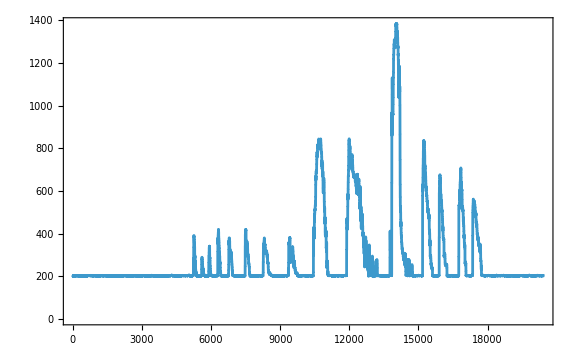
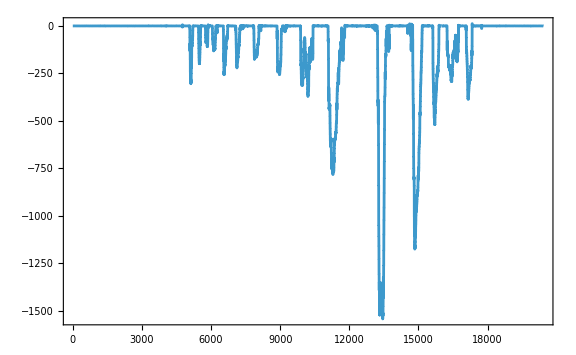
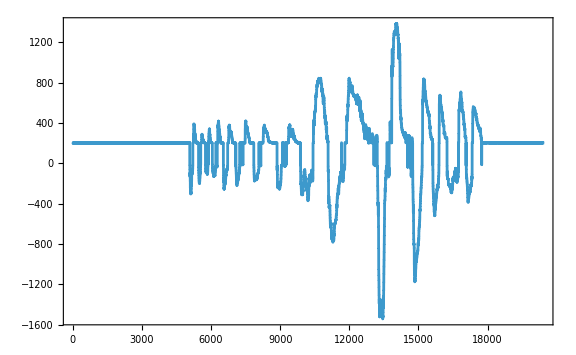

```mathematica
ListLinePlot[#,myPlotSequence[],PlotRange->All]&/@Transpose[ToExpression/@dPexa[[2;;-15]][[All,{2,-3,-2}]]]
```

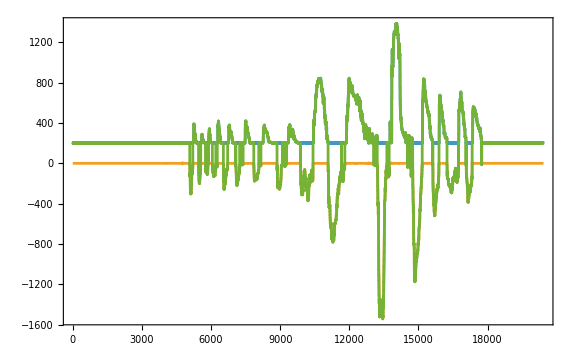

```mathematica
ListLinePlot[#,myPlotSequence[],PlotRange->All]&@Transpose[ToExpression/@dPexa[[2;;-15]][[All,{2,-3,-2}]]]
```

### lung volume

```mathematica
spiroDataPNG={"https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/13-52_files/1044169497.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/13-58_files/4099019431.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-07_files/1268081655.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-09_files/2919065533.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-12_files/1528221221.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-16_files/3867062029.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-18_files/1455467792.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-21_files/4196314456.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-25_files/3023710562.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-28_files/177688888.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-30_files/1389351546.png","https://raw.githubusercontent.com/Carl-Firle/my-data-storage/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/14-34_files/1988483359.png"};
```

2;;9

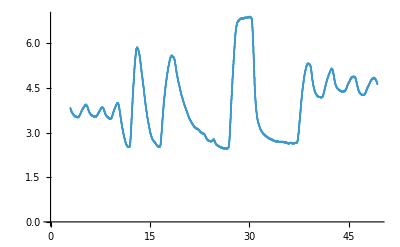

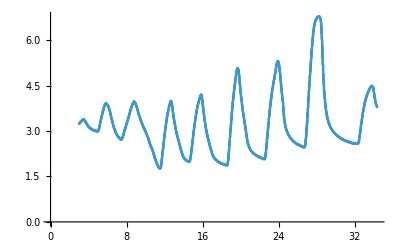

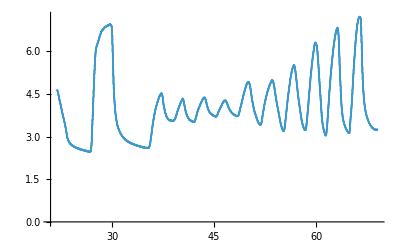

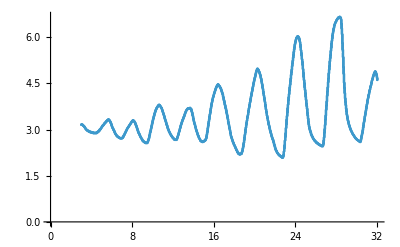

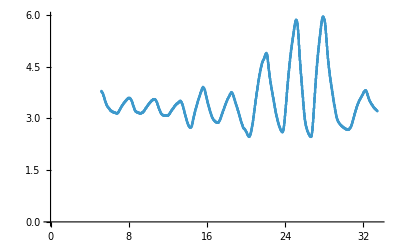

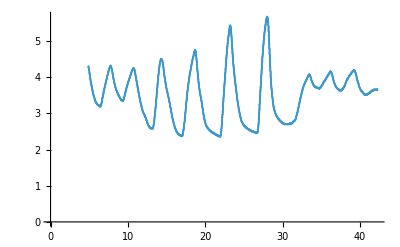

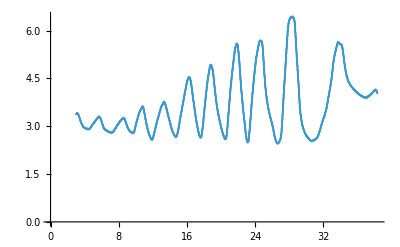

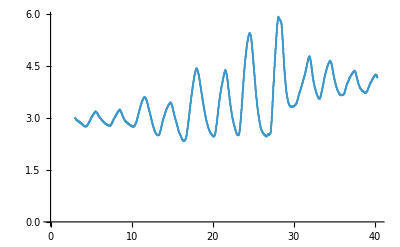

```mathematica
preparePNGData=.
preparePNGData[pngPath_String]:=Module[{points,pxPosition0And1Y,pxPosition0And2X,pxDistanceFor1Liter,pxDistanceFor1S}
,points=PixelValuePositions[Import[pngPath],Blue,.25]; (*get blue pixle points*)

pxPosition0And1Y={{85,203},{84,144}}; (*manually detected 0 and 1 y-values*)
pxPosition0And2X={{859,145},{799,145}}; (*manually detected 0 and 2 x-values*)
pxDistanceFor1Liter=Subtract@@(pxPosition0And1Yᵀ[[2]]); (*factor for volume scaling insted of pixles*)
pxDistanceFor1S=Subtract@@(pxPosition0And2Xᵀ[[1]])/2; (*factor for volume scaling insted of pixles*)

points=Select[points,#[[2]]<550& ] ;(*cut top right curve description*)
points[[All,2]]=points[[All,2]]/pxDistanceFor1Liter 1.; (*replace y pixles values by volumes values*)
points[[All,1]]=points[[All,1]]/pxDistanceFor1S 1.; (*replace x pixles values by second values*)

Print[ListPlot[points]];
SortBy[points,First]]

parts=2;;9
points=preparePNGData[#]&/@(spiroDataPNG[[parts]])
```

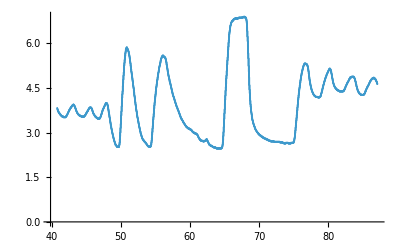
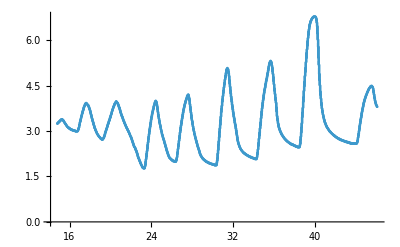
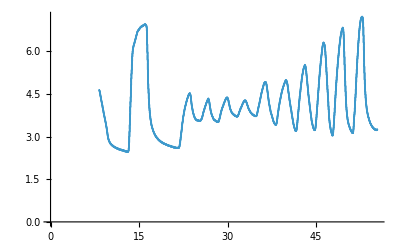
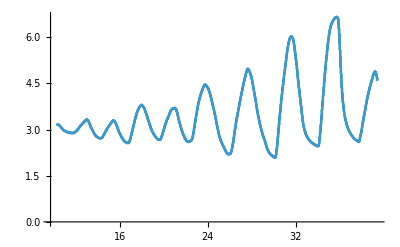
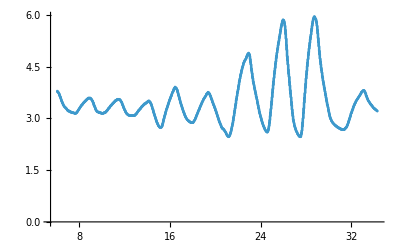
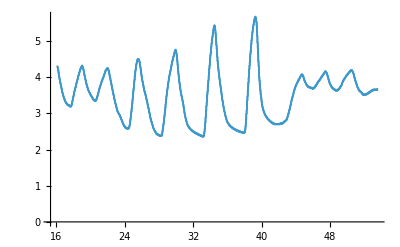
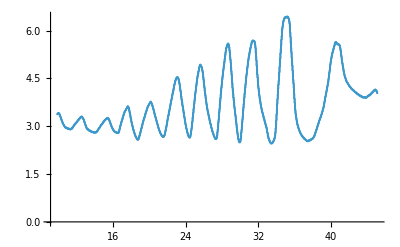
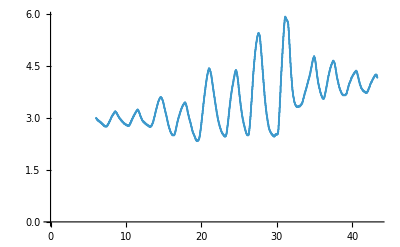

```mathematica
spiroTimeDeltaCorrection=.
spiroTimeDeltaCorrection[list_List]:=Module[{diff,lasttime,temp,tempAll},
Map[(lasttime=#[[2,-1,1]];
diff=#[[1]]-lasttime;
temp=#[[2,All,1]]+diff;
tempAll=#;
tempAll[[2,All,1]]=temp;
#[[-1]]->tempAll[[2]]
)&
,list
]
]

spiroDataTimeCalibrated=spiroTimeDeltaCorrection[Transpose[{times[[parts]][[All,-2]],points,filenames[[parts]]}]];
ListPlot[#[[2]]]&/@spiroDataTimeCalibrated
```

```mathematica
Abs[Subtract@@MinMax@#[[2,All,2]]] &/@spiroDataTimeCalibrated
```

{4.44068,5.01695,4.76271,4.59322,3.49153,3.32203,3.98305,3.59322}

```mathematica
spiroDataTimeCalibrated
```

```mathematica
smoothSpiroData=.
smoothSpiroData[l_]:=l[[1]]->((Normal[Mean[#[[All,2]]]&/@GroupBy[l[[2]],First]]) /. (Rule->List))

spiroDataTimeCalibratedSmoothed=smoothSpiroData[#]&/@spiroDataTimeCalibrated
```

### RIP data

```mathematica
allRIPData=(path="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20250327-01_rip_spiro/data-files/"~~#~~".csv";If[URLRead[path]["StatusCode"]==200,#->Import[path],Nothing])&/@filenames
```

```mathematica
TableForm[allRIPData[[-1,2,1;;5]]] (*die Datensätze wurden beim Export vom Vernier Programm zusammengehängt. Der letzte Datensatz enthält alle Messreihen!*)
```

Datensatz 1:Zeit(s) | Datensatz 1:Force 1(N) | Datensatz 1:Respiration Rate 1(bpm) | Datensatz 1:Force 2(N) | Datensatz 1:Respiration Rate 2(bpm) | Datensatz 2:Zeit(s) | Datensatz 2:Force 1(N) | Datensatz 2:Respiration Rate 1(bpm) | Datensatz 2:Force 2(N) | Datensatz 2:Respiration Rate 2(bpm) | Datensatz 3:Zeit(s) | Datensatz 3:Force 1(N) | Datensatz 3:Respiration Rate 1(bpm) | Datensatz 3:Force 2(N) | Datensatz 3:Respiration Rate 2(bpm) | Datensatz 4:Zeit(s) | Datensatz 4:Force 1(N) | Datensatz 4:Respiration Rate 1(bpm) | Datensatz 4:Force 2(N) | Datensatz 4:Respiration Rate 2(bpm) | Datensatz 5:Zeit(s) | Datensatz 5:Force 1(N) | Datensatz 5:Respiration Rate 1(bpm) | Datensatz 5:Force 2(N) | Datensatz 5:Respiration Rate 2(bpm) | Datensatz 6:Zeit(s) | Datensatz 6:Force 1(N) | Datensatz 6:Respiration Rate 1(bpm) | Datensatz 6:Force 2(N) | Datensatz 6:Respiration Rate 2(bpm) | Datensatz 7:Zeit(s) | Datensatz 7:Force 1(N) | Datensatz 7:Respiration Rate 1(bpm) | Datensatz 7:Force 2(N) | Datensatz 7:Respiration Rate 2(bpm) | Datensatz 8:Zeit(s) | Datensatz 8:Force 1(N) | Datensatz 8:Respiration Rate 1(bpm) | Datensatz 8:Force 2(N) | Datensatz 8:Respiration Rate 2(bpm) | Datensatz 9:Zeit(s) | Datensatz 9:Force 1(N) | Datensatz 9:Respiration Rate 1(bpm) | Datensatz 9:Force 2(N) | Datensatz 9:Respiration Rate 2(bpm) | Datensatz 10:Zeit(s) | Datensatz 10:Force 1(N) | Datensatz 10:Respiration Rate 1(bpm) | Datensatz 10:Force 2(N) | Datensatz 10:Respiration Rate 2(bpm) | Datensatz 11:Zeit(s) | Datensatz 11:Force 1(N) | Datensatz 11:Respiration Rate 1(bpm) | Datensatz 11:Force 2(N) | Datensatz 11:Respiration Rate 2(bpm) | Datensatz 12:Zeit(s) | Datensatz 12:Force 1(N) | Datensatz 12:Respiration Rate 1(bpm) | Datensatz 12:Force 2(N) | Datensatz 12:Respiration Rate 2(bpm) | Datensatz 13:Zeit(s) | Datensatz 13:Force 1(N) | Datensatz 13:Respiration Rate 1(bpm) | Datensatz 13:Force 2(N) | Datensatz 13:Respiration Rate 2(bpm) | Datensatz 14:Zeit(s) | Datensatz 14:Force 1(N) | Datensatz 14:Respiration Rate 1(bpm) | Datensatz 14:Force 2(N) | Datensatz 14:Respiration Rate 2(bpm) | Datensatz 15:Zeit(s) | Datensatz 15:Force 1(N) | Datensatz 15:Respiration Rate 1(bpm) | Datensatz 15:Force 2(N) | Datensatz 15:Respiration Rate 2(bpm) | Datensatz 16:Zeit(s) | Datensatz 16:Force 1(N) | Datensatz 16:Respiration Rate 1(bpm) | Datensatz 16:Force 2(N) | Datensatz 16:Respiration Rate 2(bpm) | Datensatz 17:Zeit(s) | Datensatz 17:Force 1(N) | Datensatz 17:Respiration Rate 1(bpm) | Datensatz 17:Force 2(N) | Datensatz 17:Respiration Rate 2(bpm) | Datensatz 18:Zeit(s) | Datensatz 18:Force 1(N) | Datensatz 18:Respiration Rate 1(bpm) | Datensatz 18:Force 2(N) | Datensatz 18:Respiration Rate 2(bpm) | Datensatz 19:Zeit(s) | Datensatz 19:Force 1(N) | Datensatz 19:Respiration Rate 1(bpm) | Datensatz 19:Force 2(N) | Datensatz 19:Respiration Rate 2(bpm)
0. | 14.8856 | 22.3729 | 12.2965 | 22.3577 | 0. | 10.5293 | 21.398 | 8.47167 | 21.4133 | 0. | 12.8084 | 20.7612 | 10.1018 | 20.7756 | 0. | 14.3618 | 0. | 10.9091 | 14.4578 | 0. | 16.2346 | 22.0147 | 11.2106 | 18.012 | 0. | 12.5554 | 21.9619 | 8.96478 | 21.9619 | 0. | 10.3147 | 9.91736 | 8.25705 | 9.90099 | 0. | 10.7439 | 16.632 | 9.34293 | 14.5935 | 0. | 10.0387 | 20.3313 | 7.38835 | 20.4255 | 0. | 11.2626 | 21.2598 | 7.75627 | 20.2551 | 0. | 12.6704 | 12.5174 | 8.97756 | 12.4138 | 0. | 10.5651 | 0. | 7.99644 | 0. | 0. | 12.3331 | 0 | 9.44768 | 19.4384 | 0. | 8.64626 | 0. | 7.12774 | 19.4085 | 0. | 9.85989 | 6.23701 | 7.5672 | 0 | 0. | 7.91808 | 6.85453 | 6.67551 | 14.7472 | 0. | 12.2999 | 8.79765 | 8.49467 | 17.2579 | 0. | 10.7541 | 21.7077 | 7.83037 | 20.0267 | 0. | 7.17203 | 0. | 6.34846 | 8.44278
0.1 | 13.9734 | Missing[NotAvailable] | 11.7421 | Missing[NotAvailable] | 0.1 | 11.5896 | Missing[NotAvailable] | 9.11553 | Missing[NotAvailable] | 0.1 | 11.4798 | Missing[NotAvailable] | 9.38636 | Missing[NotAvailable] | 0.1 | 12.6985 | Missing[NotAvailable] | 9.93568 | Missing[NotAvailable] | 0.1 | 16.7405 | Missing[NotAvailable] | 11.4252 | Missing[NotAvailable] | 0.1 | 14.1318 | Missing[NotAvailable] | 9.93313 | Missing[NotAvailable] | 0.1 | 9.73213 | Missing[NotAvailable] | 8.06032 | Missing[NotAvailable] | 0.1 | 9.45109 | Missing[NotAvailable] | 8.49722 | Missing[NotAvailable] | 0.1 | 11.679 | Missing[NotAvailable] | 8.25705 | Missing[NotAvailable] | 0.1 | 10.7107 | Missing[NotAvailable] | 7.79971 | Missing[NotAvailable] | 0.1 | 11.237 | Missing[NotAvailable] | 8.55598 | Missing[NotAvailable] | 0.1 | 11.0837 | Missing[NotAvailable] | 8.11141 | Missing[NotAvailable] | 0.1 | 11.5462 | Missing[NotAvailable] | 8.95712 | Missing[NotAvailable] | 0.1 | 8.19658 | Missing[NotAvailable] | 6.81603 | Missing[NotAvailable] | 0.1 | 9.47408 | Missing[NotAvailable] | 7.2376 | Missing[NotAvailable] | 0.1 | 7.59104 | Missing[NotAvailable] | 6.69083 | Missing[NotAvailable] | 0.1 | 13.0639 | Missing[NotAvailable] | 8.88814 | Missing[NotAvailable] | 0.1 | 9.90332 | Missing[NotAvailable] | 7.37813 | Missing[NotAvailable] | 0.1 | 7.20013 | Missing[NotAvailable] | 6.43533 | Missing[NotAvailable]
0.2 | 12.7036 | Missing[NotAvailable] | 10.9117 | Missing[NotAvailable] | 0.2 | 13.0996 | Missing[NotAvailable] | 9.97146 | Missing[NotAvailable] | 0.2 | 10.1052 | Missing[NotAvailable] | 8.67352 | Missing[NotAvailable] | 0.2 | 10.772 | Missing[NotAvailable] | 8.70928 | Missing[NotAvailable] | 0.2 | 16.7865 | Missing[NotAvailable] | 11.415 | Missing[NotAvailable] | 0.2 | 16.135 | Missing[NotAvailable] | 11.0011 | Missing[NotAvailable] | 0.2 | 9.13426 | Missing[NotAvailable] | 7.81248 | Missing[NotAvailable] | 0.2 | 8.06883 | Missing[NotAvailable] | 7.50077 | Missing[NotAvailable] | 0.2 | 13.7614 | Missing[NotAvailable] | 9.34037 | Missing[NotAvailable] | 0.2 | 10.0106 | Missing[NotAvailable] | 7.70773 | Missing[NotAvailable] | 0.2 | 9.54307 | Missing[NotAvailable] | 7.96067 | Missing[NotAvailable] | 0.2 | 11.0658 | Missing[NotAvailable] | 8.12164 | Missing[NotAvailable] | 0.2 | 10.4859 | Missing[NotAvailable] | 8.2826 | Missing[NotAvailable] | 0.2 | 7.71624 | Missing[NotAvailable] | 6.45833 | Missing[NotAvailable] | 0.2 | 9.36421 | Missing[NotAvailable] | 6.87735 | Missing[NotAvailable] | 0.2 | 7.58849 | Missing[NotAvailable] | 6.76237 | Missing[NotAvailable] | 0.2 | 13.5519 | Missing[NotAvailable] | 9.13086 | Missing[NotAvailable] | 0.2 | 8.79189 | Missing[NotAvailable] | 6.8518 | Missing[NotAvailable] | 0.2 | 7.43008 | Missing[NotAvailable] | 6.78537 | Missing[NotAvailable]
0.3 | 12.0623 | Missing[NotAvailable] | 10.4084 | Missing[NotAvailable] | 0.3 | 14.0271 | Missing[NotAvailable] | 10.393 | Missing[NotAvailable] | 0.3 | 9.91354 | Missing[NotAvailable] | 8.57642 | Missing[NotAvailable] | 0.3 | 10.4015 | Missing[NotAvailable] | 8.35414 | Missing[NotAvailable] | 0.3 | 16.02 | Missing[NotAvailable] | 11.0292 | Missing[NotAvailable] | 0.3 | 17.0292 | Missing[NotAvailable] | 11.2566 | Missing[NotAvailable] | 0.3 | 9.07294 | Missing[NotAvailable] | 7.70006 | Missing[NotAvailable] | 0.3 | 7.9513 | Missing[NotAvailable] | 7.26315 | Missing[NotAvailable] | 0.3 | 14.7604 | Missing[NotAvailable] | 9.64442 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.54676 | Missing[NotAvailable] | 0.3 | 9.11893 | Missing[NotAvailable] | 7.53654 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.88402 | Missing[NotAvailable] | 0.3 | 9.93143 | Missing[NotAvailable] | 8.03477 | Missing[NotAvailable] | 0.3 | 7.71368 | Missing[NotAvailable] | 6.48132 | Missing[NotAvailable] | 0.3 | 9.8139 | Missing[NotAvailable] | 6.93101 | Missing[NotAvailable] | 0.3 | 8.49807 | Missing[NotAvailable] | 7.03065 | Missing[NotAvailable] | 0.3 | 12.8876 | Missing[NotAvailable] | 8.87791 | Missing[NotAvailable] | 0.3 | 8.25279 | Missing[NotAvailable] | 6.72916 | Missing[NotAvailable] | 0.3 | 7.95386 | Missing[NotAvailable] | 7.32958 | Missing[NotAvailable]

```mathematica
ripData=Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,All,{1,2,4}]]}]
```

```mathematica
ripData=#[[1]]->#[[2]]&/@(Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,2;;-1,{1,2,4}]]}]/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
```

```mathematica
Transpose[{ filenames,times}]
```

{{13-52,{0.,11.587,86.626,163.838}},{13-58,{0.,10.215,87.148,96.617}},{14-07,{0.,7.21,46.161,95.607}},{14-09,{0.,6.607,55.385,76.168}},{14-12,{0.,6.155,39.394,51.1}},{14-16,{0.,4.767,34.314,45.389}},{14-18,{0.,16.13,53.533,60.223}},{14-21,{0.,5.265,45.151,69.111}},{14-25,{0.,4.027,43.35,48.236}},{14-28,{0.,4.538,32.585,48.87}},{14-30,{0.,4.698,34.442,48.932}},{14-34,{0.,18.158,64.024,77.825}}}

```mathematica
{#[[1]],#[[2,-1,1]]}&/@(ripData/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
(*die Zeiten der RIP Messungen sind "Taktgeber" und synchron*)
```

{{13-52,163.2},{13-58,95.9},{14-07,94.8},{14-09,75.5},{14-18,59.4},{14-21,68.5},{14-28,48.2},{14-30,48.1},{14-34,77.1}}

### Evaluation

```mathematica
Length@spiroDataTimeCalibratedSmoothed
Length@ripData
spiroDataTimeCalibratedSmoothed[[All,1]]
ripData[[All,1]]
evaluableData=Intersection[spiroDataTimeCalibrated[[All,1]],ripData[[All,1]]]
```

8

9

{13-58,14-07,14-09,14-12,14-16,14-18,14-21,14-25}

{13-52,13-58,14-07,14-09,14-18,14-21,14-28,14-30,14-34}

{13-58,14-07,14-09,14-18,14-21}

```mathematica
calibrateXMin=.
calibrateXMin[spiro_List]:=Module[{lowestVolumes,lowestForce}
,lowestVolumes=Min[spiro[[All,2]]]
]
calibrateXMin[spiroDataTimeCalibratedSmoothed[[-1,2]]]
```

2.33051

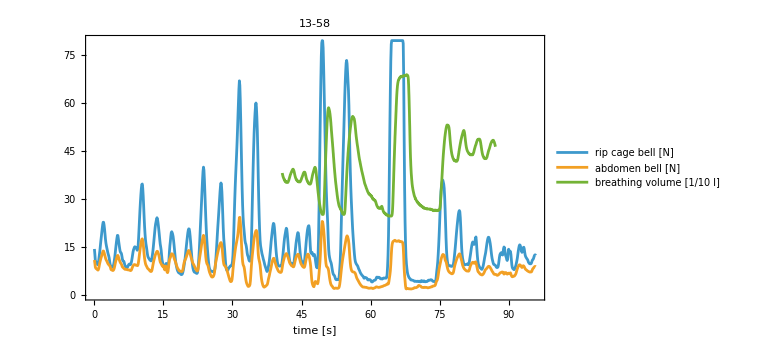
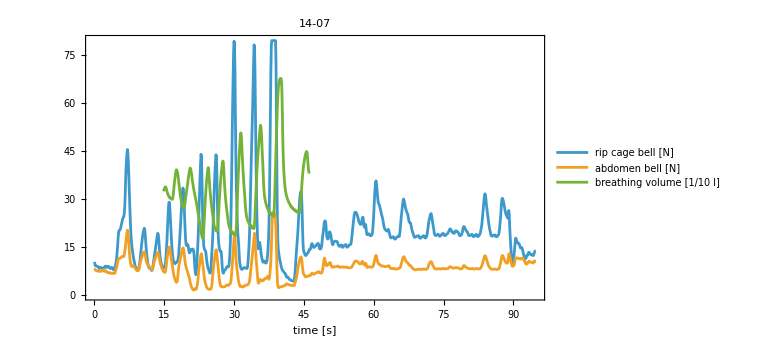
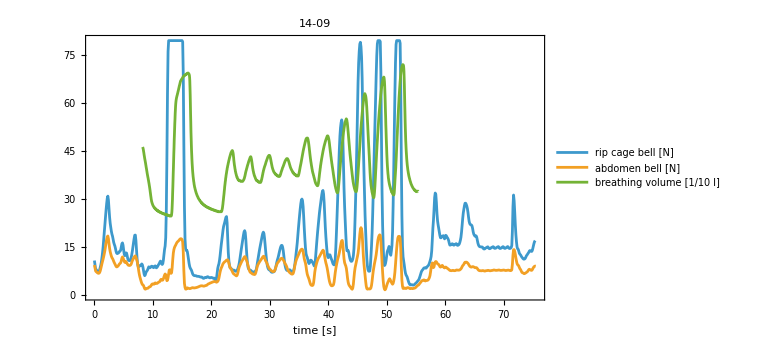
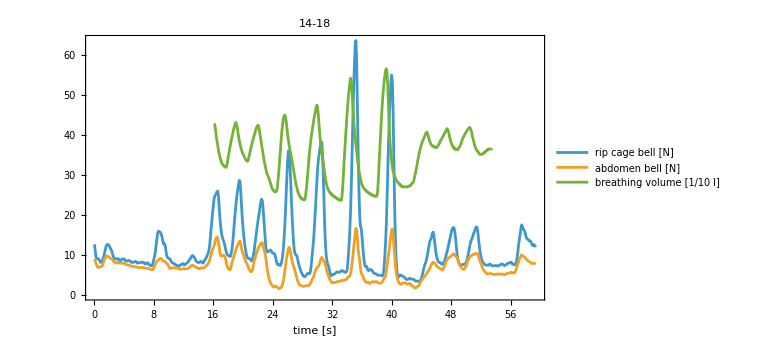
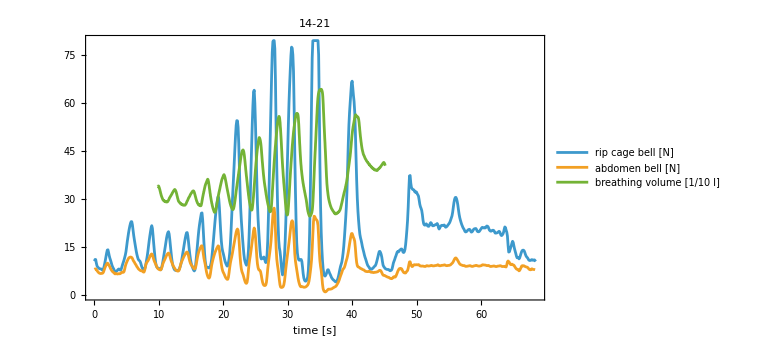

```mathematica
dataForAnalysis=Transpose[{evaluableData,evaluableData/.ripData,evaluableData /. spiroDataTimeCalibratedSmoothed}];
dataForAnalysis[[All,2]]=Map[Transpose[{{#[[1]],#[[2]]},{#[[1]],#[[3]]}}&/@(Flatten[#,1])] /. Missing["NotAvailable"]->Null&,dataForAnalysis[[All,{2}]]];

ListPlot[Append[#[[2]],{#[[1]],#[[2]]*10}&/@#[[3]]],PlotLabel->myStyle@#[[1]],PlotRange->All,PlotLegends->{"rip cage bell [N]","abdomen bell [N]","breathing volume [1/10 l]"},FrameLabel->{"time [s]",None},ImageSize->Large,Frame->True,Joined->True,myFrameStyle[],myFrameTickStyle[], myPlotStyle[]]&/@dataForAnalysis
```

```mathematica
dataForAnalysis={#[[1]],Append[#[[2]],#[[3]]]}&/@dataForAnalysis (*time stamp, {rip, abdomen, spiro}*)
```

{{{41.8813,3.51695},{43.1813,3.9322}},{{44.5147,3.5339},{45.648,3.83898}},{{46.8147,3.4661},{47.9147,3.99153}},{{49.6147,2.51695},{50.8813,5.85593}},{{54.2147,2.51695},{56.1147,5.58475}},{{64.2147,2.4661},{67.8147,6.88136}},{{74.4147,2.63559},{76.6813,5.31356}},{{78.648,4.17797},{80.248,5.14407}},{{81.9147,4.38136},{83.5813,4.87288}},{{84.9813,4.26271},{86.648,4.83898}}}

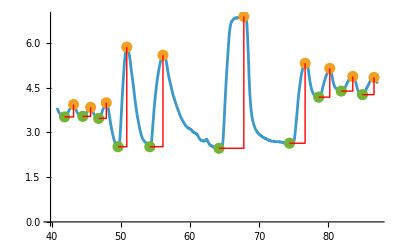

```mathematica
values=dataForAnalysis[[1,2,3]];
peaks=FindPeaks[dataForAnalysis[[1,2,3]][[All,2]],10];
peaksLow=FindPeaks[-dataForAnalysis[[1,2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}]
xdiffsLine={#[[1]],{#[[2,1]],
#[[1,2]]},#[[2]]}&/@xdiffs;
linesDiff=Line/@xdiffsLine;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}]

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All}
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
```

breaths from spirometry

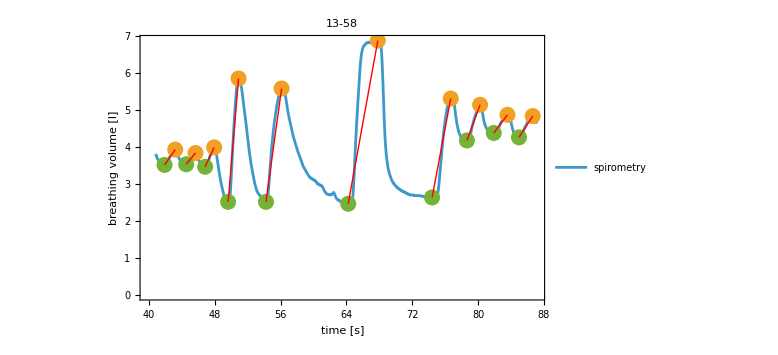
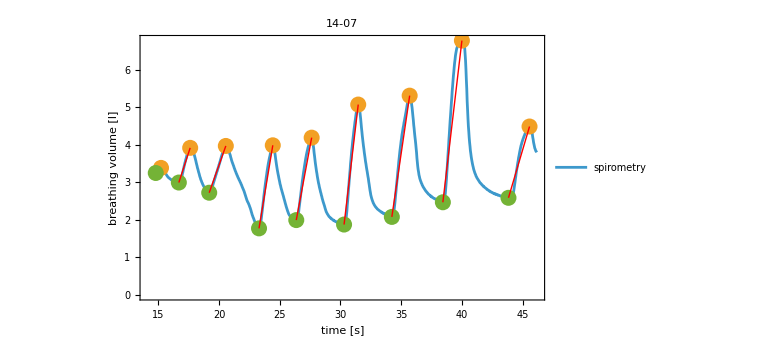
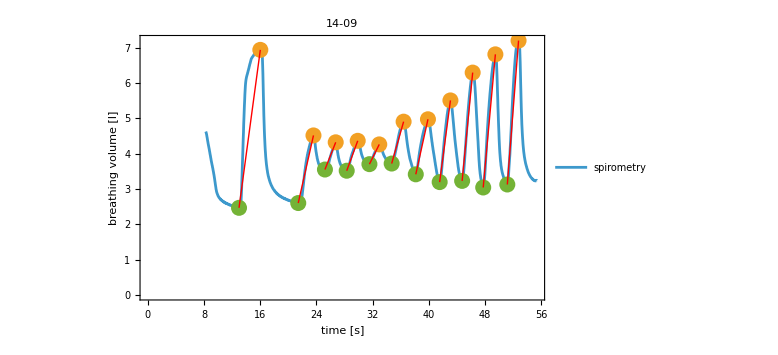
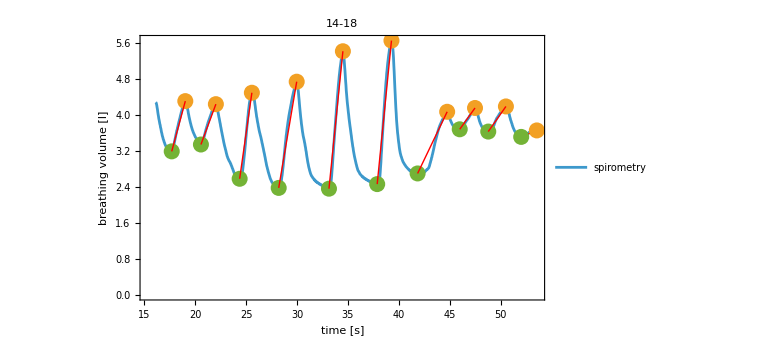
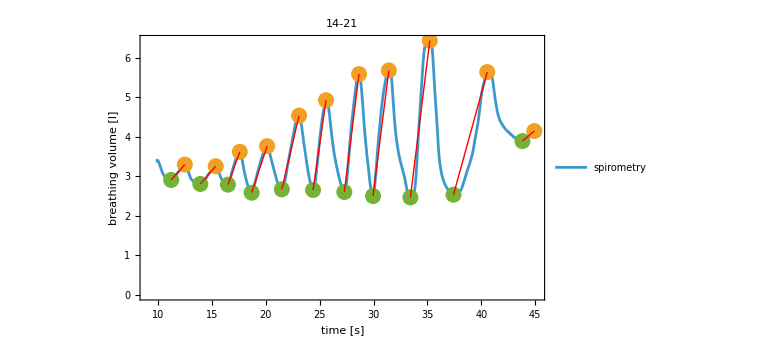

```mathematica
breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,values=l[[2,3]];
peaks=FindPeaks[l[[2,3]][[All,2]],10];
peaksLow=FindPeaks[-l[[2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}],

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],PlotLegends->{"spirometry"},FrameLabel->{"time [s]","breathing volume [l]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]}
]

spiroBreaths=breathDetect/@ dataForAnalysis
```

breaths from RIP

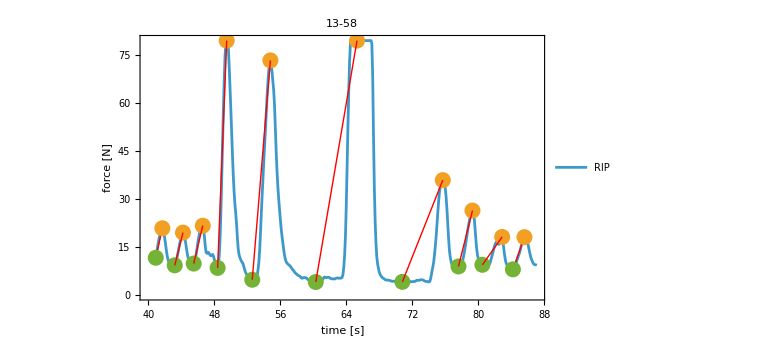
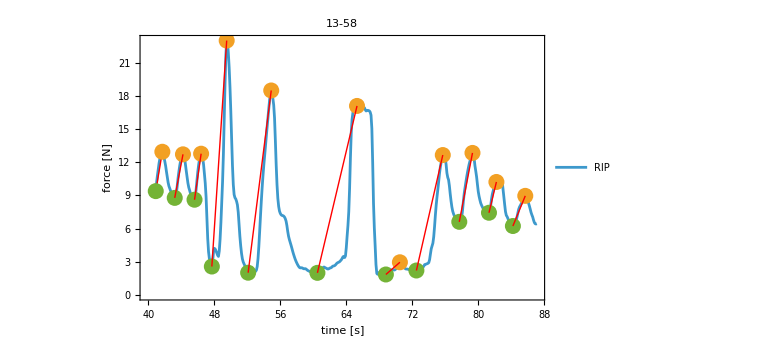
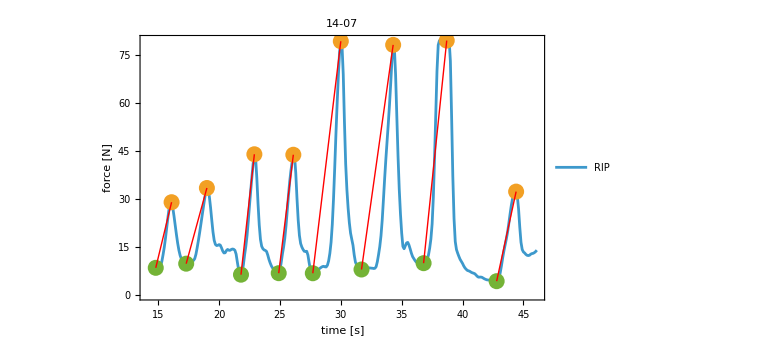
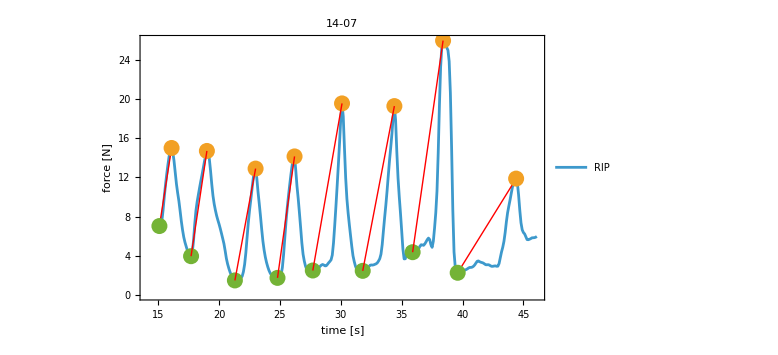
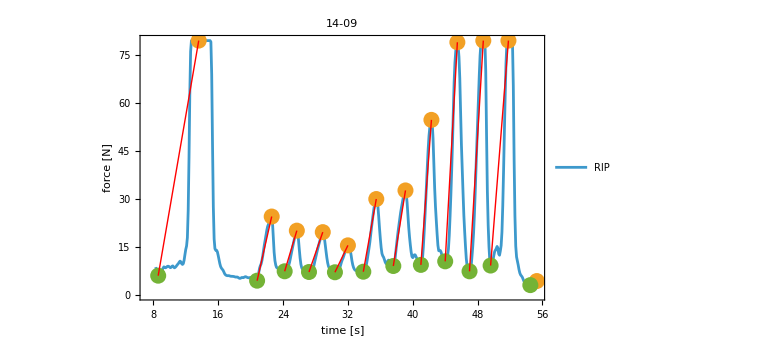
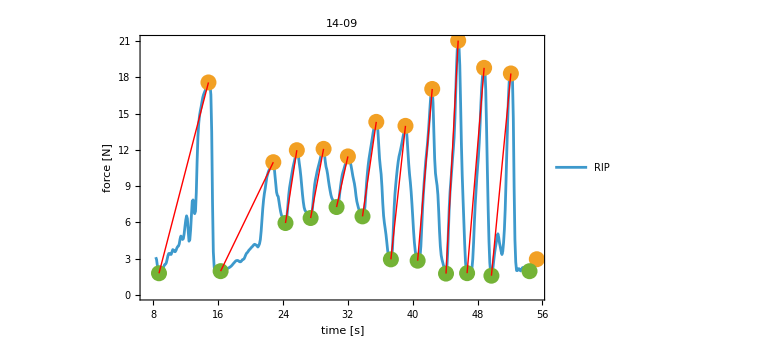
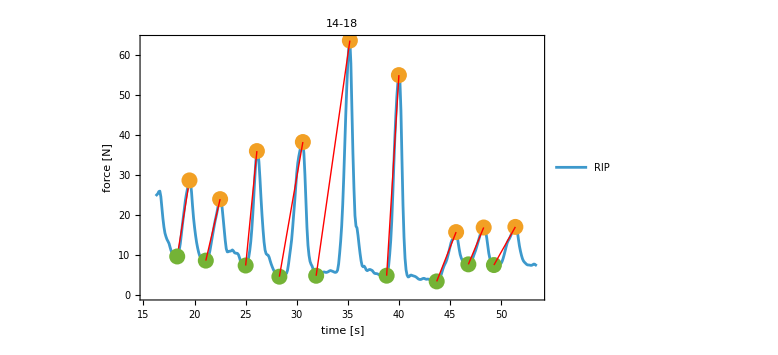
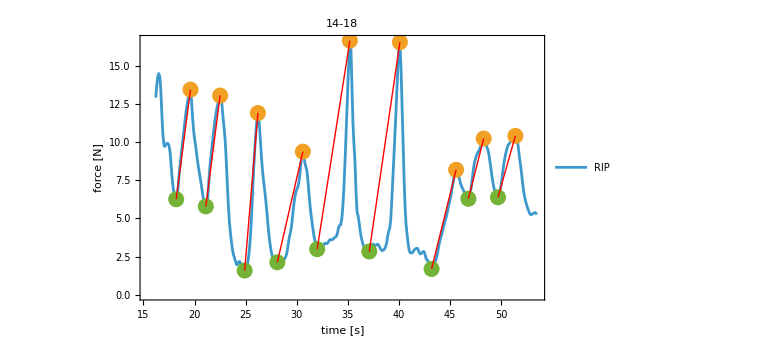

```mathematica
dataForAnalysisCropped=dataForAnalysis;
Table[
{lbound,ubound}=dataForAnalysisCropped[[i,2,3]][[{1,-1}]][[All,1]];
dataForAnalysisCropped[[i,2,1]]=Select[dataForAnalysisCropped[[i,2,1]],lbound<#[[1]]<ubound&];
dataForAnalysisCropped[[i,2,2]]=Select[dataForAnalysisCropped[[i,2,2]],lbound<#[[1]]<ubound&];
,{i,Length@dataForAnalysisCropped}];

breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,
Table[values=l[[2,i]];
peaks=FindPeaks[l[[2,i]][[All,2]],6];
peaksLow=FindPeaks[-l[[2,i]][[All,2]],6];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)
(*hier noch prüfen, ob der Peak im Zeitverlauf auch nahe am Peak der Spirometrie liegt!!! 10%?*)
peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ force [N]"}]
,Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],
PlotLegends->{"RIP"},FrameLabel->{"time [s]","force [N]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,PlotRange->All,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
}
,{i,{1,2}}]

]

ripBreaths=breathDetect/@dataForAnalysisCropped
```

```mathematica
Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]
```

{{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}}}

```mathematica
dCorrelation=Flatten/@Transpose[{spiroBreaths[[All,1]],ripBreaths[[All,All,1]]}]
```

{{,,},{,,},{,,},{,,},{,,}}

```mathematica
myTabularNormal=.
myTabularNormal[t_]:=Module[{},If[TabularQ[t],Values/@(Normal@t),Values/@(Normal/@t)]]
```

```mathematica
spiroBreaths[[1,2]]
```

-Graphics-

```mathematica
myPlotLabelAndLegend[plotLabel_,plotLegend_List,frameLabel_List]:=Sequence[PlotLabel->myStyle@plotLabel,
PlotLegends->myStyle/@plotLegend,FrameLabel->frameLabel]
```

```mathematica
myPlotConfig=.
myPlotConfig=Sequence[PlotRange->All,Frame->True,ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]
```

Sequence[PlotRange→All,Frame→True,ImageSize→Large,FrameStyle→Directive[FontSize→15,FontFamily→Lucida Sans Unicode,GrayLevel[0]],FrameTicksStyle→Directive[FontSize→15,FontFamily→Lucida Sans Unicode,GrayLevel[0]]]

```mathematica
myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP"},{"force [N]","breathing volume [l]"}]
```

Sequence[PlotLabel→13-58,PlotLegends→{correlation spirometry and RIP},FrameLabel→{force [N],breathing volume [l]}]

{10,10,10}

{{{1.3,0.8,0.8},{0.415254,9.22866,3.55912}},{{1.13333,1.,1.},{0.305085,10.2353,3.93726}},{{1.1,1.1,0.8},{0.525424,11.845,4.15954}},{{1.26667,1.1,1.8},{3.33898,71.1057,20.4221}},{{1.9,2.2,2.8},{3.0678,68.6171,16.4721}},{{3.6,5.,4.8},{4.41525,75.5309,15.0873}},{{2.26667,4.9,3.2},{2.67797,31.8302,10.4372}},{{1.6,1.7,1.6},{0.966102,17.4915,6.22909}},{{1.66667,2.4,0.9},{0.491525,8.71255,2.78239}},{{1.66667,1.4,1.5},{0.576271,10.0641,2.72619}}}

FittedModel[…]

{0.0659819+0.0512292 x-2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2),0.0659819+0.0512292 x+2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2)}

{,}

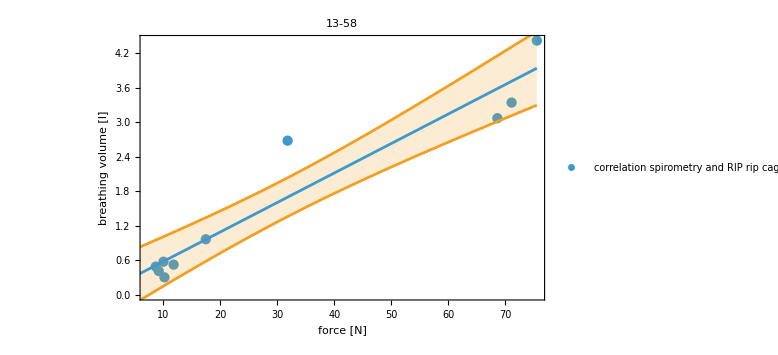

```mathematica
temp=myTabularNormal[dCorrelation[[1]]];
temp[[3]] = Select[temp[[3]],#[[2]]>1.5&];
Length/@temp
temp=Transpose/@Transpose[temp]
lnm=LinearModelFit[temp[[All,2]][[All,{2,1}]],x,x]
lnm["MeanPredictionBands",ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[temp[[All,2]][[All,{2,1}]],myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@temp[[All,2]][[All,{2,1}]],Max@temp[[All,2]][[All,{2,1}]]},Filling->{2->{1}}]]
```

manuelle Anpassung, siehe auch Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]

13 - 58 delete 7 bei abdomen
14-07 delete 1 bei spiro
14 - 09 delete - 1 bei cage und abdomen
14 - 18 delete - 1 bei spirometry
14-21 delete -1 bei spirometry und cage

```mathematica
evaluableData
```

{13-58,14-07,14-09,14-18,14-21}

```mathematica
dCorrelationElected=myTabularNormal/@dCorrelation;
dCorrelationElected=Delete[dCorrelationElected,{{1,3,7},{2,1,1},{3,2,-1},{3,3,-1},{4,1,-1},{5,1,-1},{5,2,-1}}];
Map[Length,dCorrelationElected,{2}]
dCorrelationElected=myFlatten[Transpose[dCorrelationElected][[All,All,All,2]],1];
```

{{10,10,10},{8,8,8},{11,11,11},{9,9,9},{10,10,10}}

FittedModel[…]

FittedModel[…]

{0.90628,0.904242}

0.156586

{{0.181881+0.0487349 x-2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2),0.181881+0.0487349 x+2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2)},}

{,}

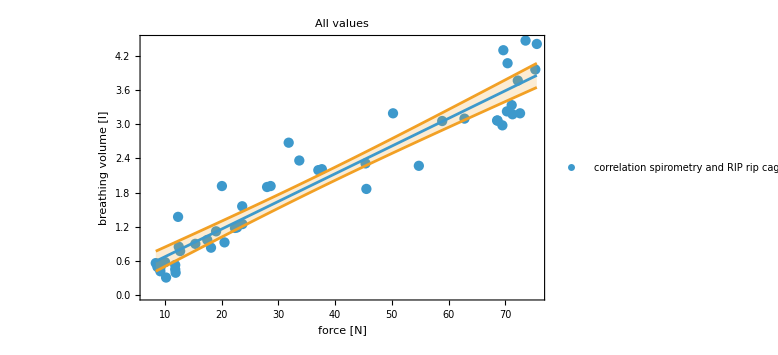

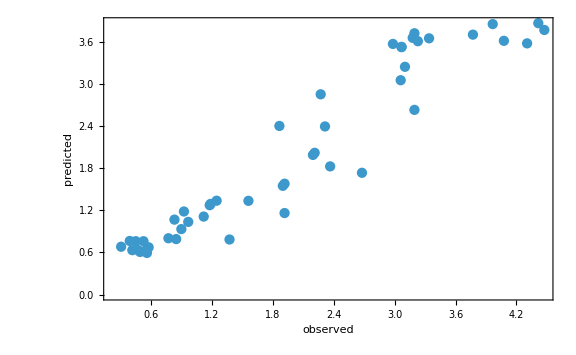

```mathematica
lnmRipCageGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,2}]]],x,x] (*volume in Newton out*)
fitData=Transpose[dCorrelationElected[[{2,1}]]];
lnmRipCageGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95] (*https://www.graphpad.com/support/faqid/1506/  Prediciton = wo die nächsten Datenpunkte mit 95% Wahrscheinlichkeit liegen werden, Confidence = wo die aktuellen Daten zu 95% liegen and https://en.wikipedia.org/wiki/Confidence_and_prediction_bands#Prediction_bands*)
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
Min@fitData[[All,1]]
```

8.41872

FittedModel[…]

FittedModel[…]

{0.773369,0.768442}

0.37865

{{-0.123767+0.187762 x-2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2),-0.123767+0.187762 x+2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2)},}

{,}

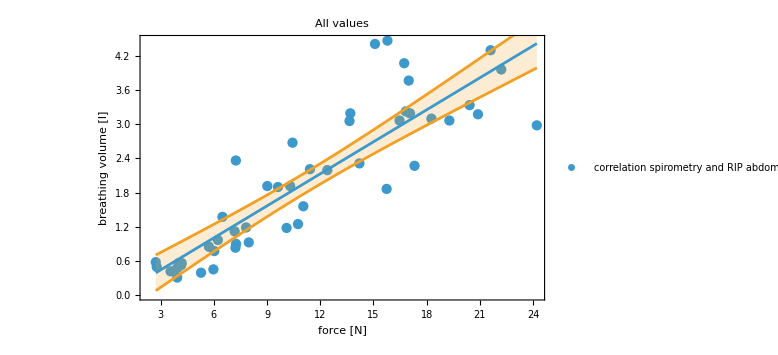

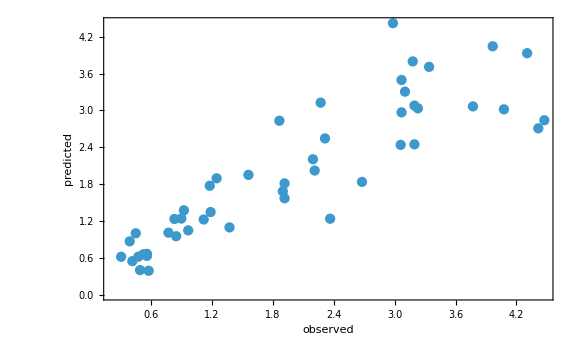

```mathematica
lnmAbdomenGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,3}]]],x,x]
fitData=Transpose[dCorrelationElected[[{3,1}]]];
lnmAbdomenGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP abdomen"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
newtonFromRIPripcage=.
newtonFromRIPripcage[v_]:=Module[{},Around[lnmRipCageGetForce[v],(Subtract@@Reverse@(lnmRipCageGetForce["MeanPredictionBands",ConfidenceLevel->.95] /. x->v))/2]]
{#,newtonFromRIPcage[#]}&/@{3,5}
```

{{3,newtonFromRIPcage[3]},{5,newtonFromRIPcage[5]}}

```mathematica
volumeFromRIPripcage=.
volumeFromRIPripcage[f_]:=Module[{},Around[lnmRipCageGetVolume[f],(Subtract@@Reverse@(lnmRipCageGetVolume["MeanPredictionBands",ConfidenceLevel->.95] /. x->f))/2]]
{#,newtonFromRIPcage[#]}&/@{20,40,60}
```

{{20,newtonFromRIPcage[20]},{40,newtonFromRIPcage[40]},{60,newtonFromRIPcage[60]}}

-Graphics--Graphics-
aus
 https://publikationen.dguv.de/widgets/pdf/download/article/1011%7CDGUV-Regel112-190_Benutzung-von-Atemschutzgeraeten_Download.pdf

Zielwerte: 30 und 50 l/min  Atemminutenvolumen

```mathematica
af=Range[10,70,5] (*Atemfrequenz*)
```

{10,15,20,25,30,35,40,45,50,55,60,65,70}

```mathematica
Print[myStyle["values for 30 l/min"]]
TableForm[{af,30./af,newtonFromRIPripcage/@(30./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 30 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70
breathing volume [l] | 3. | 2. | 1.5 | 1.2 | 1. | 0.857143 | 0.75 | 0.666667 | 0.6 | 0.545455 | 0.5 | 0.461538 | 0.428571
force of RIP of ripcage [N] | 55.92.9 | 37.32.2 | 28.02.4 | 22.42.7 | 18.72.9 | 16.03.0 | 14.03.1 | 12.53.3 | 11.33.3 | 10.23.4 | 9.43.5 | 8.73.5 | 8.4.

```mathematica
Print[myStyle["values for 50 l/min"]]
TableForm[{af,50./af,newtonFromRIPripcage/@(50./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 50 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70
breathing volume [l] | 5. | 3.33333 | 2.5 | 2. | 1.66667 | 1.42857 | 1.25 | 1.11111 | 1. | 0.909091 | 0.833333 | 0.769231 | 0.714286
force of RIP of ripcage [N] | 93.6. | 62.13.3 | 46.62.4 | 37.32.2 | 31.12.3 | 26.72.5 | 23.32.6 | 20.82.7 | 18.72.9 | 17.03.0 | 15.63.0 | 14.43.1 | 13.43.2

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 30 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[30,{#[[1]]-#[[2]]corr,#[[1]]+#[[2]]corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 30 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 50 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[50,{#[[1]]-#[[2]] corr,#[[1]]+#[[2]] corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 50 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate